```mathematica
AppendTo[$Path,"C:\\Program Files\\Wolfram Research\\Mathematica\\LevelScheme-3.53"];
Get["LevelScheme`"]
ruru={m->4.3 10^6,G->6.67 10^-8,tM->rg/(60 cc)(*min/M*),rg->(G m Msun)/cc^2,dd->8.4 10^3 pc,arcsec->(2 π dd)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};ruru=Thread[ruru[[All,1]]->(ruru[[All,2]]//.ruru)]
```

```mathematica
rurux={G->6.67 10^-8,tM->rg/(60 cc)(*min/M*),rg->(G m Msun)/cc^2,dd->8.4 10^3 pc,arcsec->(2 π dd)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};rurux=Thread[rurux[[All,1]]->(rurux[[All,2]]//.rurux)]
Print["Frequency ν=",νx=118,"Hz for 10Msun BH ⇒ τ=",1/(νx 10/m)/60/.m->4.3 10^6,"min for Sgr A^*"]
Print["For GROJ1655-40: main period = ",νν=300(*450*),"Hz = ",Round[(cc/rg)/νf/.rurux/.{m->6.3,νf->νν}],"M"]
Print["For XTEJ1550-564: main period = ",νν=276,"Hz = ",Round[(cc/rg)/νf/.rurux/.{m->9.1,νf->νν}],"M"]
Print["For GRS1915+105: main period = ",νν=168,"Hz = ",Round[(cc/rg)/νf/.rurux/.{m->10.1,νf->νν}],"M"]
Print["For Cyg X1: ν_2 period = ",νν=135,"Hz = ",Round[(cc/rg)/νf/.rurux/.{m->14.8,νf->νν}],"M"]
sug={z1->1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3)),z2->(3 a^2+z1^2)^(1/2),risco->3+z2-((3-z1)(3+z1+2z2))^(1/2)};
sug=Thread[sug[[All,1]]->(sug[[All,2]]//.sug)];
Print["BH rotational frequency"]
Ωbh=FullSimplify[M^(1/2)/((risco M)^(3/2)+a M^(3/2)),M>0];Print["Orbital timescale t_orb=",torb=Simplify[(2π)/(Ωbh M)rg/cc,M>0]](*formula 9*);
Print["ISCO frequency for 10M_sunBH: ν_ISCO=",1/torb/.sug/.ruru/.m->10/.a->0.0, "Hz for non-spinning BH"]
Print["ISCO frequency for 10M_sunBH: ν_ISCO=",1/torb/.sug/.ruru/.m->10/.a->0.94, "Hz for spin a=0.94"]

t0=rg/cc/60/.ruru/.m->4.3 10^6
t0CK=3.4/4.3 rg/cc/60/.ruru/.m->4.3 10^6
Print["t0Dole=",t0Dole=4.5/4.3 rg/cc/60/.ruru/.m->4.3 10^6]
11/t0CK/.m->4.3 10^6
17/t0/.m->4.3 10^6
{23,28,45}/t0/.m->4.3 10^6
2.75 60/t0/.m->4.3 10^6
{6,7,9}/t0Dole/.m->4.3 10^6
60/17 48./.m->4.3 10^6
```

```mathematica
QPOs
```

-Graphics--Graphics--Graphics-
RMS amplitude 1-2%

## VLA data

```mathematica
dat11=Import["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\VLA_10May2008X.dat"];
datt=dat11[[All,1;;2]];
```

```mathematica
{ListPlot[datt,ImageSize->500],ListPlot[MovingAverage[datt,30],ImageSize->500]}
```

```mathematica
fluxes=datt[[All,2]];tim=datt[[All,1]];
sffun[ddt_,func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{ddt n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{tim,fluxes}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[0.0009,fluxes],PlotRange->{0.002,0.07}]}]
```

```mathematica
inter=Interpolation[datt,InterpolationOrder->1]
tmin=tim[[1]];tmax=tim[[-1]];
timer=Range[tmin,tmax,0.0009];
newdata=inter[timer];
```

```mathematica
Length[newdata]
Length[datt]
```

```mathematica
GraphicsRow[{ListPlot[Transpose[{timer,newdata}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[60 0.0009,newdata],PlotRange->{0.002,0.07}]}]
```

```mathematica
Δt=0.2;
NIntegrate[(inter[t+Δt]-inter[t])^2,{t,tmin,tmax-Δt}]
```

## Jon simulation thickdisk7 - to paper

### Units for paper

```mathematica
Print["Minutes per M: ", tM/.ruru]
Print["Periods in M: ",{6,7,9,17,23,28,45,2.75*60}(*min*)/tM/.ruru," ",{35}/tM/.ruru]
170tM/.ruru
```

```mathematica
180/π ArcCos[0.9]
```

0.94 1.5517 2.4840 0.16992 147780.66084 1.003 e - 08
Temperature - 3.2*10^10K at 6M

```mathematica
Print["Best angle = ",180/π(π-2.4840),"deg"]
Log[10,10^3]
Log[10,1.2]
```

```mathematica
35(1+√(1-a^2)/.a->1)/(1+√(1-a^2)/.a->0.9375)
```

### Periodograms for Olek’s simulations - spin 0, 0.7, 0.9

```mathematica
Dynamic[fnum]
Ntodx=10.;
angles={{"Oleka0","th214lo","poliresa0th214fn",12424,22424},{"Oleka07","th260lo","poliresa70th260fn",4204,9204},{"Oleka09","th252lo","poliresa90th252fn",2376,4876}};
Do[dix[1]="E:\\GRMHD\\Oleka0\\spectra\\"<>angles[[1,1]]<>"\\",{o,Length[angles]}]
dix[2]="E:\\GRMHD\\Oleka07\\spectra\\"<>angles[[2,1]]<>"\\";
dix[3]="E:\\GRMHD\\Oleka09\\spectra\\"<>angles[[3,1]]<>"\\";
Do[dix[o]="E:\\GRMHD\\"<>angles[[o,1]]<>"\\spectra\\"<>angles[[o,2]]<>"\\";fil=dix[o]<>"totspec.dat";
If[FileExistsQ[fil],impx[o]=Get[fil],impx[o]=Table[Import[dix[o]<>angles[[o,3]]<>ToString[fnum]<>"boo.dat"],{fnum,angles[[o,4]],angles[[o,5]]}];Put[impx[o],fil]];
lop[o]=Length[impx[o]],{o,Length[angles]}]
coe=1;kmin=3;kmax=9;kstep=3;
nums=Ntodx impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];
Dimensions[impx[1]]
Dimensions[impx[2]]
Dimensions[impx[3]]
```

```mathematica
Do[means[3,fr,th]=Mean[impx[th][[All,fr,3]]];means[4,fr,th]=means[3,fr,th];means[5,fr,th]=means[3,fr,th];means[6,fr,th]=90,{th,1,Length[angles]},{fr,1,Length[impx[1][[1]]]}]

SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^4.;(*Papadakis & Lawrence (1993)*)
autovar[typ_,mu_,fr_,th_]:=(mult=mu;binned=(impx[th][[All,fr,typ]])/means[typ,fr,th];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=Ntodx ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[typ,fr,th]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=Ntodx ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
ttx=TimeUsed[];
{Dynamic[th],Dynamic[typ],Dynamic[fr],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{50,tmax},All}];
typ=.;fr=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};
Do[Do[autovar[typ,3.0,fr,th];
resx[typ,fr,th]=Join[res[typ,fr,th],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr,th]],{A x+B},{A,B},x];
resx[typ,fr,th]=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr,th][[1,1]])res[typ,fr,th][[1,2]]}&/@{4,8},resx[typ,fr,th]];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx[typ,fr,th]],InterpolationOrder->1];
PSDfluxx[typ,fr,th]=ListLogLogPlot[resx[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr,th];
nux=154;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat";
If[!FileExistsQ[nam],tabresy[typ,fr,th]=Table[randx=(RandomVariate[NormalDistribution[],lop[th]]+ⅈ RandomVariate[NormalDistribution[],lop[th]])√Exp[interand[Log[Ntodx lop[th]/Range[lop[th]]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];Put[tabresy[typ,fr,th],nam],tabresy[typ,fr,th]=Get[nam]];
Do[ress[aa]=tabresy[typ,fr,th][[aa]],{aa,nux}];
ressmean[typ,fr,th]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr,th]=ListLogLogPlot[ressmean[typ,fr,th],PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDflux[typ,fr,th]=ListLogLogPlot[res[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
resstot[typ,fr,th]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
ressmax[typ,fr,th]=Transpose[{resst,Mean[{RankedMax[#,3]&/@resstot[typ,fr,th],RankedMax[#,4]&/@resstot[typ,fr,th]}]}];
ressmin[typ,fr,th]=Transpose[{resst,Mean[{RankedMin[#,3]&/@resstot[typ,fr,th],RankedMin[#,4]&/@resstot[typ,fr,th]}]}];
PSDFmin[typ,fr,th]=ListLogLogPlot[ressmin[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr,th]=ListLogLogPlot[ressmax[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];,{fr,kmin,kmax,kstep}],{typ,3,6},{th,1,Length[angles]}]
Print["Computed in ",TimeUsed[]-ttx,"s"](*367s for 1σ ⇒ 2218s(37min) for 2σ ⇒ 36121s(10hrs) for 3σ*)
(*Dimensions[tabresy[3,3]]
Do[Put[tabresy[typ,fr,th],nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat"],{fr,kmin,kmax,kstep},{typ,3,6}]*)
```

```mathematica
th=1;grgr=GraphicsGrid[Table[sh[typ,fr,th]=Show[{PSDflux[typ,fr,th],PSDFmax[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]}],{typ,3,6},{fr,1,3}]]
th=.;
```

```mathematica
grgr=GraphicsGrid[Table[sh[typ,fr,1]=Show[{PSDflux[typ,fr,1],PSDFmax[typ,fr,1],PSDFrandmean[typ,fr,1],PSDfluxx[typ,fr,1]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
grgr=GraphicsGrid[Table[sh[typ,fr,2]=Show[{PSDflux[typ,fr,2],PSDFmax[typ,fr,2],PSDFrandmean[typ,fr,2],PSDfluxx[typ,fr,2]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
grgr=GraphicsGrid[Table[sh[typ,fr,3]=Show[{PSDflux[typ,fr,3],PSDFmax[typ,fr,3],PSDFrandmean[typ,fr,3],PSDfluxx[typ,fr,3]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
```

```mathematica
lk=Length[resst];lx=Length[resx[3,3,1]];mx=1/30.;
shift[2]=Table[{1,1},{i,lk}];shix[2]=Table[{1,1},{i,lx}];
shift[1]=Table[{1,1/mx},{i,lk}];shix[1]=Table[{1,1/mx},{i,lx}];
shift[3]=Table[{1,mx},{i,lk}];shix[3]=Table[{1,mx},{i,lx}];
Thread[{fllab[3],fllab[4],fllab[5],fllab[6]}={"Flux at ","LP at ","EVPA at ","CP at "}];
Thread[{frlab[1],frlab[2],frlab[3],frlab[6],frlab[9]}={"22GHz","43GHz","87GHz","230GHz","857GHz"}];
mysize=16;
figvx=Figure[
{ScaledLabel[{0.21,0.76},"Top - spin 0",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.21,0.74},"Middle - spin 0.7",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.21,0.72},"Bottom - spin 0.9",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
Multipanel[{{0,1},{0,1}},{3,3},XPlotRanges->{Log10[20],Log10[tmax]},YPlotRanges->{{Log10[10^-7],Log10[10^2.5]},{Log10[10^-4],Log10[10^3.5]},{Log10[10^-2],Log10[10^5.5]}},
FontSize->mysize,BufferB->4,XFrameLabels->{"Period T [M]"},BufferL->6,YFrameLabels->"Periodogram   I(T)",
YFrameTicks->LogTicks[-10,10],XFrameTicks->LogTicks[-10,10,TickLabelStep->1],
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
SetOptions[DataSymbol,SymbolSize->0.001],
SetOptions[DataLine,Thickness->1.5],
SetOptions[DataValues,AxisScaling->{Log,Log}],Table[{FigurePanel[{typ-2,fr/3},PanelLetter->None],pan[typ,fr]=Table[{DataPlot[shift[th]res[typ,fr,th],DataLine->{Color->Black}],DataPlot[shift[th]ressmean[typ,fr,th],DataLine->{Color->Black,Dashing->7}],DataPlot[shift[th]ressmax[typ,fr,th],DataLine->{Color->Red}],
DataPlot[shix[th]resx[typ,fr,th],DataLine->{Color->Green,Dashing->5}]},{th,3}];lab[typ,fr]=fllab[typ]<>frlab[fr];sclab[typ,fr]=ScaledLabel[{0.18,0.89},lab[typ,fr],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold];pan[typ,fr],sclab[typ,fr]},{typ,3,5},{fr,kmin,kmax,kstep}]},
PlotRange->{{-0.07,1.01},{-0.07,1.01}},ImageSize->{1300,800}]
```

```mathematica
Export["C:\\study\\accretion\\! 2013 1spring UMD\\Long time variability\\allspins_high_f_2sigma.eps",figvx]
```

```mathematica
Export["C:\\study\\accretion\\! 2013 1spring UMD\\Long time variability\\spin0_low_f.eps",figvx]
```

```mathematica
Export["C:\\study\\accretion\\! 2013 1spring UMD\\Long time variability\\spin0_high_f.eps",figvx]
```

### Periodograms for Olek’s simulations - spin 0, incl. low frequency modeling

```mathematica
ν=86 10^9;(*Hz*)ν0=(ee B)/(2π me cc);
Bsolx=Solve[2 B^2/(8π)==ρ[Log[r]] kb Tp[r]/.solful,B][[2]]/.ruru;
xm=(2ν)/(3ν0)(mp/me cs[Log[r]]^2)^-2/.ruru/.Bsolx;eqIRx=4.43 10^-30 4π ρ[Log[r]]ν 4.0505/xm^(1/6)(1+0.4/xm^(1/4)+0.5316/xm^(1/2))Exp[-1.8899 xm^(1/3)](4π)/3 r^3 rg^3/BesselK[2,me/mp cs[Log[r]]^-2]==(LIRx=2π ν^2/cc^2 kb Te[r]4π r^2 rg^2/.ruru/.solful)/.solful/.ruru;rIRx=FindRoot[eqIRx,{r,10}];
```

```mathematica
Dynamic[fnum]
angles={{"th214lo","poliresa0th214fn",12424,22424}};
dix[1]="E:\\GRMHD\\Oleka0\\spectra\\"<>angles[[1,1]]<>"\\";
Do[dir0="E:\\GRMHD\\Oleka0\\spectra\\"<>angles[[o,1]]<>"\\";
fil=dir0<>"totspec.dat";
If[FileExistsQ[fil],impx[o]=Get[fil],impx[o]=Table[Import[dir0<>angles[[o,2]]<>ToString[fnum]<>"boo.dat"],{fnum,angles[[o,3]],angles[[o,4]]}];Put[impx[o],fil]],{o,Length[angles]}]
coe=1;kmin=3;kmax=9;kstep=3;
nums=10impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];
Dimensions[impx[1]]
```

```mathematica
Do[means[3,fr,th]=Mean[impx[th][[All,fr,3]]];means[4,fr,th]=means[3,fr,th];means[5,fr,th]=means[3,fr,th];means[6,fr,th]=90,{th,1,Length[angles]},{fr,1,Length[impx[1][[1]]]}]

SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^4.;(*Papadakis & Lawrence (1993)*)
autovar[typ_,mu_,fr_,th_]:=(mult=mu;binned=(impx[th][[All,fr,typ]])/means[typ,fr,th];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[typ,fr,th]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
ttx=TimeUsed[];
{Dynamic[th],Dynamic[fr],Dynamic[typ],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{50,tmax},All}];
typ=.;fr=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};
Do[Do[autovar[typ,3.0,fr,th];
resx[typ,fr,th]=Join[res[typ,fr,th],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr,th]],{A x+B},{A,B},x];
resx[typ,fr,th]=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr,th][[1,1]])res[typ,fr,th][[1,2]]}&/@{4,8},resx[typ,fr,th]];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx[typ,fr,th]],InterpolationOrder->1];
PSDfluxx[typ,fr,th]=ListLogLogPlot[resx[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr,th];
nux=22;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat";
If[!FileExistsQ[nam],tabresy[typ,fr,th]=Table[randx=(RandomVariate[NormalDistribution[],10000]+ⅈ RandomVariate[NormalDistribution[],10000])√Exp[interand[Log[100001/Range[10000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];Put[tabresy[typ,fr,th],nam],tabresy[typ,fr,th]=Get[nam]];
Do[ress[aa]=tabresy[typ,fr,th][[aa]],{aa,nux}];
ressmean[typ,fr,th]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr,th]=ListLogLogPlot[ressmean[typ,fr,th],PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDflux[typ,fr,th]=ListLogLogPlot[res[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
resstot[typ,fr,th]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
ressmax[typ,fr,th]=Transpose[{resst,Mean[{RankedMax[#,3]&/@resstot[typ,fr,th],RankedMax[#,4]&/@resstot[typ,fr,th]}]}];
ressmin[typ,fr,th]=Transpose[{resst,Mean[{RankedMin[#,3]&/@resstot[typ,fr,th],RankedMin[#,4]&/@resstot[typ,fr,th]}]}];
PSDFmin[typ,fr,th]=ListLogLogPlot[ressmin[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr,th]=ListLogLogPlot[ressmax[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];,{fr,kmin,kmax,kstep}],{typ,3,6},{th,1,Length[angles]}]
Print["Computed in ",TimeUsed[]-ttx,"s"](*367s for 1σ ⇒ 2218s(37min) for 2σ ⇒ 36121s(10hrs) for 3σ*)
(*Dimensions[tabresy[3,3]]
Do[Put[tabresy[typ,fr,th],nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat"],{fr,kmin,kmax,kstep},{typ,3,6}]*)
```

```mathematica
th=1;grgr=GraphicsGrid[Table[sh[typ,fr,th]=Show[{PSDflux[typ,fr,th],PSDFmax[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]}],{typ,3,6},{fr,1,3}]]
th=.;
```

```mathematica
th=1;grgr=GraphicsGrid[Table[sh[typ,fr,th]=Show[{PSDflux[typ,fr,th],PSDFmax[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
th=.;
```

```mathematica
lk=Length[resst];lx=Length[resx[3,3,1]];mx=1/30.;
shift[1]=Table[{1,1},{i,lk}];shix[1]=Table[{1,1},{i,lx}];
shift[2]=Table[{1,1/mx},{i,lk}];shix[2]=Table[{1,1/mx},{i,lx}];
shift[3]=Table[{1,mx},{i,lk}];shix[3]=Table[{1,mx},{i,lx}];
Thread[{fllab[3],fllab[4],fllab[5],fllab[6]}={"Flux at ","LP at ","EVPA at ","CP at "}];
Thread[{frlab[1],frlab[2],frlab[3],frlab[6],frlab[9]}={"22GHz","43GHz","87GHz","230GHz","857GHz"}];
mysize=16;
figvx=Figure[
{ScaledLabel[{0.21,0.76},"Top - face-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.21,0.74},"Middle - general inclination",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.21,0.72},"Bottom - edge-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
Multipanel[{{0,1},{0,1}},{3,3},XPlotRanges->{Log10[20],Log10[tmax]},YPlotRanges->{{Log10[10^-6],Log10[10]},{Log10[10^-3],Log10[300]},{Log10[0.1],Log10[10^4]}},
FontSize->mysize,BufferB->4,XFrameLabels->{"Period T [M]"},BufferL->6,YFrameLabels->"Periodogram   I(T)",
YFrameTicks->LogTicks[-10,10],XFrameTicks->LogTicks[-10,10,TickLabelStep->1],
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
SetOptions[DataSymbol,SymbolSize->0.001],
SetOptions[DataLine,Thickness->1.5],
SetOptions[DataValues,AxisScaling->{Log,Log}],Table[{FigurePanel[{typ-2,fr(*/3*)},PanelLetter->None],pan[typ,fr]=Table[{DataPlot[shift[th]res[typ,fr,th],DataLine->{Color->Black}],DataPlot[shift[th]ressmean[typ,fr,th],DataLine->{Color->Black,Dashing->7}],DataPlot[shift[th]ressmax[typ,fr,th],DataLine->{Color->Red}],
DataPlot[shix[th]resx[typ,fr,th],DataLine->{Color->Green,Dashing->5}]},{th,1}];lab[typ,fr]=fllab[typ]<>frlab[fr];sclab[typ,fr]=ScaledLabel[{0.18,0.89},lab[typ,fr],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold];pan[typ,fr],sclab[typ,fr]},{typ,3,5},{fr,1,3(*kmin,kmax,kstep*)}]},
PlotRange->{{-0.07,1.01},{-0.07,1.01}},ImageSize->{1300,800}]
```

```mathematica
Export["C:\\study\\accretion\\! 2013 1spring UMD\\Long time variability\\spin0_low_f.eps",figvx]
```

```mathematica
Export["C:\\study\\accretion\\! 2013 1spring UMD\\Long time variability\\spin0_high_f.eps",figvx]
```

### Comparison of periodogram for fast light vs. correct radiative transfer - substantial differences found!

```mathematica
Dynamic[fnum]
angles={"th248lo","th248fast"};
dix[1]="E:\\GRMHD\\thickdisk7\\spectra\\"<>angles[[1]]<>"\\";
dix[2]="E:\\GRMHD\\thickdisk7\\spectra\\"<>angles[[2]]<>"\\";
Do[dir0="E:\\GRMHD\\thickdisk7\\spectra\\"<>angles[[o]]<>"\\";
fil=dir0<>"totspec.dat";
If[FileExistsQ[fil],impx[o]=Get[fil],impx[o]=Table[Import[dir0<>"poliresa93.75th248fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999}];Put[impx[o],fil]],{o,Length[angles]}]
coe=1;kmin=3;kmax=9;kstep=3;
nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];
Dimensions[impx[1]]
Dimensions[impx[2]]
```

```mathematica
Do[means[3,fr,th]=Mean[impx[th][[All,fr,3]]];means[4,fr,th]=means[3,fr,th];means[5,fr,th]=means[3,fr,th];means[6,fr,th]=90,{th,1,2},{fr,kmin,kmax,kstep}]

SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;(*Papadakis & Lawrence (1993)*)
autovar[typ_,mu_,fr_,th_]:=(mult=mu;binned=(impx[th][[All,fr,typ]])/means[typ,fr,th];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[typ,fr,th]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
ttx=TimeUsed[];
{Dynamic[th],Dynamic[fr],Dynamic[typ],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{20,1500},All}];
typ=.;fr=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};
Do[Do[autovar[typ,3.0,fr,th];
resx[typ,fr,th]=Join[res[typ,fr,th],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr,th]],{A x+B},{A,B},x];
resx[typ,fr,th]=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr,th][[1,1]])res[typ,fr,th][[1,2]]}&/@{4,8},resx[typ,fr,th]];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx[typ,fr,th]],InterpolationOrder->1];
PSDfluxx[typ,fr,th]=ListLogLogPlot[resx[typ,fr,th],PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr,th];
nux=22;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat";
If[!FileExistsQ[nam],tabresy[typ,fr,th]=Table[randx=(RandomVariate[NormalDistribution[],5000]+ⅈ RandomVariate[NormalDistribution[],5000])√Exp[interand[Log[20000/Range[5000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];Put[tabresy[typ,fr,th],nam],tabresy[typ,fr,th]=Get[nam]];
Do[ress[aa]=tabresy[typ,fr,th][[aa]],{aa,nux}];
ressmean[typ,fr,th]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr,th]=ListLogLogPlot[ressmean[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDflux[typ,fr,th]=ListLogLogPlot[res[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
resstot[typ,fr,th]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
ressmax[typ,fr,th]=Transpose[{resst,Mean[{RankedMax[#,3]&/@resstot[typ,fr,th],RankedMax[#,4]&/@resstot[typ,fr,th]}]}];
ressmin[typ,fr,th]=Transpose[{resst,Mean[{RankedMin[#,3]&/@resstot[typ,fr,th],RankedMin[#,4]&/@resstot[typ,fr,th]}]}];
PSDFmin[typ,fr,th]=ListLogLogPlot[ressmin[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr,th]=ListLogLogPlot[ressmax[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];,{fr,kmin,kmax,kstep}],{typ,3,6},{th,1,2}]
Print["Computed in ",TimeUsed[]-ttx,"s"](*367s for 1σ ⇒ 2218s(37min) for 2σ ⇒ 36121s(10hrs) for 3σ*)
(*Dimensions[tabresy[3,3]]
Do[Put[tabresy[typ,fr,th],nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat"],{fr,kmin,kmax,kstep},{typ,3,6}]*)
```

```mathematica
{PSDflux[3,6,1],PSDflux[3,3,1],PSDflux[4,6,1]}
{PSDflux[3,6,2],PSDflux[3,3,2],PSDflux[4,6,2]}
```

```mathematica
GraphicsGrid[Table[Show[{PSDflux[typ,fr,1],PSDflux[typ,fr,2]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
```

```mathematica
th=2;grgr=GraphicsGrid[Table[sh[typ,fr,th]=Show[{PSDflux[typ,fr,th],PSDFmax[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
th=.;
```

### Figure QPOcurve.eps

```mathematica
fnum=.;{Dynamic[o],Dynamic[fnum]}
angles={"th248lo","th296lo","th174lo","th248lo120phi","th248lo240phi"};

Do[dir0="E:\\GRMHD\\thickdisk7\\spectra\\"<>angles[[o]]<>"\\";
fil=dir0<>"totspec.dat";
If[FileExistsQ[fil],impx[o]=Get[fil],impx[o]=Table[Import[dir0<>"poliresa93.75"<>StringTake[angles[[o]],{1,5}]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999}];Put[impx[o],fil]],{o,1,5}]
nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];Dimensions[impx[1]]
(*coe=1;
impx[1]=Get["E:\\GRMHD\\thickdisk7\\spectra\\th248lo\\totspec.dat"];nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];Dimensions[impx[1]]
impx[2]=Get["E:\\GRMHD\\thickdisk7\\spectra\\th296lo\\totspec.dat"];Dimensions[impx[2]]
impx[3]=Get["E:\\GRMHD\\thickdisk7\\spectra\\th174lo\\totspec.dat"];Dimensions[impx[3]]*)
```

```mathematica
shi=.;
tab120=Table[Norm[impx[1][[1;;-1-shi,6,3]]-impx[4][[1+shi;;-1,6,3]]],{shi,0,30}];
tab240=Table[Norm[impx[1][[1;;-1-shi,6,3]]-impx[5][[1+shi;;-1,6,3]]],{shi,0,30}];
ListPlot[{tab120,tab240},Joined->True,PlotStyle->{Red,Blue},Frame->True,PlotLabel->"Shift 120deg and 240deg manifest at 7 and 14 minima"]
fr=6;
Flpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,1,5}],FrameLabel->{"t [GM/c^3]","F_ν [Jy]"},PlotStyle->{Blue,White(*Red*),White(*Green*),Brown,Black},Joined->True]&/@{{25500,26100}}
GraphicsGrid[{{Flpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],FrameLabel->{"t [GM/c^3]","F_ν [Jy]"}],
LPpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,4]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],PlotRange->{0,11.5},FrameLabel->{"t [GM/c^3]","LP [%]"}]},
{EVPApl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,5]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],FrameLabel->{"t [GM/c^3]","EVPA [deg]"}],
CPpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,6]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],FrameLabel->{"t [GM/c^3]","CP [%]"}]}}]&/@{{25500,26100}}
```

```mathematica
(*Making figure QPOcurve.eps*)
fr=6;typ=4;freqs[[fr]]
SetOptions[ListPlot,ImageSize->550,InterpolationOrder->1,Frame->True,Joined->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{{Black,AbsoluteThickness[2]},{Black,AbsoluteDashing[7],AbsoluteThickness[2]},{Black,AbsoluteDashing[2],AbsoluteThickness[2]}},BaseStyle->{16,"Times",Bold}];
(*Table[ListPlot[Fltr[[1+1000i;;1000(i+1)]],Joined->True,InterpolationOrder->2,ImageSize->450],{i,4}];*)
(*Table[GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,3]]}][[1+1000i;;1000(i+1)]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}][[1+1000i;;1000(i+1)]],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}][[1+1000i;;1000(i+1)]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}][[1+1000i;;1000(i+1)]],Joined->True]}}],{i,0,4}]*)
GraphicsGrid[{{Flpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],FrameLabel->{"t [GM/c^3]","F_ν [Jy]"}],
LPpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,4]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],PlotRange->{0,11.5},FrameLabel->{"t [GM/c^3]","LP [%]"}]},
{EVPApl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,5]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],FrameLabel->{"t [GM/c^3]","EVPA [deg]"}],
CPpl=ListPlot[Table[Transpose[{nums,impx[i][[All,fr,6]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{i,3}],FrameLabel->{"t [GM/c^3]","CP [%]"}]}}]&/@{{25500,26100}};

(*best times fr=6: tmin=25500;tmax=26100: 
{{13000,13400},{23400,23800},{25000,25400},{25500,25900}}*)
mysize=16;
figv=Figure[
{ScaledLabel[{0.76,0.94},"General inclination",Color->Black,FontFamily->"Times",FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.86,0.83},"Face-on",Color->Black,FontFamily->"Times",FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.86,0.805},"Edge-on",Color->Black,FontFamily->"Times",FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
Multipanel[{{0,1},{0,1}},{4,1},XPlotRanges->{{25500,26100}},YPlotRanges->{{2.55,3.36},{0.01,10},{0.1,179.9},{-2.39,+0.44}},
XFrameLabels->{"t [M]"},BufferB->4,YFrameLabels->{"F_ν [Jy]","LP [%]","EVPA [deg]","CP [%]"},BufferL->5,TickFontSize->mysize,FontSize->mysize,
(*XFrameTicks->{LinTicks[0,20,5,5],None},YFrameTicks->{{LinTicks[-6,6,3,2],None},{LinTicks[-6,6,3,2],None}},XPanelSizes->{1,0.2},YPanelSizes->{1,1},XGapSizes->{0.03},YGapSizes->{0},*)
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,(*TickNudge->{-5,{-5,0},0,0},*)FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->"(a)"],RawGraphics[Flpl,Layer->0],
FigurePanel[{2,1},PanelLetter->"(b)"],RawGraphics[LPpl,Layer->0],
FigurePanel[{3,1},PanelLetter->"(c)"],RawGraphics[EVPApl,Layer->0],
FigurePanel[{4,1},PanelLetter->"(d)"],RawGraphics[CPpl,Layer->0]},
PlotRange->{{-0.2,1.1},{-0.08,1.04}},ImageSize->{450,800}]
(*Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\QPOcurve.eps",figv]*)
(*Blue,Red,Green, {"th248","th296","th174"}*)
```

### Figure QPOfreq.eps

```mathematica
coe=1;
impx[1]=Get["E:\\GRMHD\\thickdisk7\\spectra\\th248lo\\totspec.dat"];nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];Dimensions[impx[1]]
```

```mathematica
(*GraphicsGrid[{{Flpl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],FrameLabel->{"t [GM/c^3]","F_ν [Jy]"}],
LPpl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,4]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],PlotRange->{0,11.5},FrameLabel->{"t [GM/c^3]","LP [%]"}]},
{EVPApl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,5]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],FrameLabel->{"t [GM/c^3]","EVPA [deg]"}],
CPpl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,6]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],FrameLabel->{"t [GM/c^3]","CP [%]"}]}}]&/@{{25500,26100}}*)
```

```mathematica
(*Making figure QPOfreq.eps*)
fr=.;kmin=3;kmax=9;kstep=3;
SetOptions[ListPlot,ImageSize->550,InterpolationOrder->1,Frame->True,Joined->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{{Blue,AbsoluteThickness[2]},{Red,AbsoluteDashing[7],AbsoluteThickness[2]},{Green,AbsoluteDashing[3],AbsoluteThickness[2]}},BaseStyle->{16,"Times",Bold}];
GraphicsGrid[{{Flpl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],FrameLabel->{"t [M]","F_ν [Jy]"}],
LPpl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,4]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],PlotRange->{0,14},FrameLabel->{"t [M]","LP [%]"}]},
{EVPApl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,5]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],FrameLabel->{"t [M]","EVPA [deg]"}],
CPpl=ListPlot[Table[Transpose[{nums,impx[1][[All,fr,6]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],{fr,kmin,kmax,kstep}],FrameLabel->{"t [M]","CP [%]"}]}}]&/@{{25500,26100}};

(*best times fr=6: tmin=25500;tmax=26100: 
{{13000,13400},{23400,23800},{25000,25400},{25500,25900}}*)
mysize=16;
figv=Figure[
{ScaledLabel[{0.55,0.95},"857GHz",Color->Green,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.55,0.865},"230GHz",Color->Red,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.55,0.8},"87GHz",Color->Blue,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
Multipanel[{{0,1},{0,1}},{4,1},XPlotRanges->{{25500,26100}},YPlotRanges->{{1.7,3.9},{0.1,13.9},{0.1,179.9},{-2.29,-0.19}},
XFrameLabels->{"t [M]"},BufferB->4,YFrameLabels->{"F_ν [Jy]","LP [%]","EVPA [deg]","CP [%]"},BufferL->5,TickFontSize->mysize,FontSize->mysize,
(*XFrameTicks->{LinTicks[0,20,5,5],None},YFrameTicks->{{LinTicks[-6,6,3,2],None},{LinTicks[-6,6,3,2],None}},XPanelSizes->{1,0.2},YPanelSizes->{1,1},XGapSizes->{0.03},YGapSizes->{0},*)
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,(*TickNudge->{-5,{-5,0},0,0},*)FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->"(a)"],RawGraphics[Flpl,Layer->0],
FigurePanel[{2,1},PanelLetter->"(b)"],RawGraphics[LPpl,Layer->0],
FigurePanel[{3,1},PanelLetter->"(c)"],RawGraphics[EVPApl,Layer->0],
FigurePanel[{4,1},PanelLetter->"(d)"],RawGraphics[CPpl,Layer->0]},
PlotRange->{{-0.2,1.1},{-0.08,1.04}},ImageSize->{450,800}]
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\QPOfreq.eps",figv]
(*YPlotRanges->{{2.91,3.14},{0.1,9.9},{30.1,59},{-1.99,-1.36}},*)
```

```mathematica
Options[ScaledLabel]
```

### Figure imagetotal.eps

```mathematica
func[m_]:=Quiet[dir="E:\\GRMHD\\thickdisk7\\movies\\";
namefile="E:\\GRMHD\\thickdisk7\\images\\th296\\"<>"shotimag93.75th296f230fn"<>ToString[m]<>"_501.dat";
fi11=OpenRead[namefile,BinaryFormat->True];
params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];
(*freqtab=Partition[BinaryReadList[fi11,"Real64",2 (flen+1)],2];*)
inten=BinaryReadList[fi11,"Real64"];
partres=Partition[Partition[inten,5],nxy+1];
Close[fi11];nana=ToString[Round[100 a]]<>"th"<>StringJoin[ToString[#]&/@PadLeft[IntegerDigits[Round[100 params[[2]]]],3]]<>"f"<>ToString[nu]<>"s"<>ToString[4m]<>".jpg";nameQU=dir<>"shotQUa"<>nana;
(*scI=-9.;scL=-11.1;scV=4 10^-6.;(*ν=102GHz*)*)
scI=-7.1;scL=-8.9;conlum=3;conLP=2.0;scV=13 10^-6.;(*ν=231GHz for th238*)
scI=-7.1;scL=-8.6;conlum=2.5;conLP=2.5;scV=13 10^-6.;(*ν=231GHz for th296*)
(*scI=-5.6;scL=-6.8;scV=7 10^-6.;conlum=9;conLP=2.5;(*ν=857GHz for th238*)*)
ord=1;csc=1.0;sss=0.6;plpoi=200;plpoi=200;Nlines=30;
(*conlum=10;*)cLP=0.95;
li=ListInterpolation[Log[10^-10+partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];csc=1;
totI[m]=DensityPlot[rr=(li[y,x]-scI)/Log[conlum]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},ImageSize->400,PlotPoints->plpoi,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->20}(*,Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,    θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.92}],{0,0},{1,0},Background->Black]}*),ClippingStyle->Automatic];
(*totV=DensityPlot[res=linV[y,x],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->800,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)*)
totQU[m]=VectorDensityPlot[{A=linQ[y,x];B=linU[y,x];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-cLP sss maxy,cLP sss maxy},{y,-cLP sss maxy,cLP sss maxy},VectorPoints->Nlines,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->Nlines,StreamScale->Full,MaxRecursion->2,ImageSize->400,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y,x]^2+linU[y,x]^2]-scL)/Log[conLP]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->20}(*,Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}*)];{totI[m],totQU[m]}];
Dynamic[j]
pltab=Table[func[j],{j,6380,6404,6}];
(*pltab={func[6380]}*)
```

```mathematica
(*grfl=GraphicsRow[pltab[[All,1]]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\imageflux.eps",grfl,"AllowRasterization"->True, ImageResolution->150]
grLP=GraphicsRow[pltab[[All,2]]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\imageLP.eps",grLP,"AllowRasterization"->True, ImageResolution->150]*)
ratio=0.34;ysc=10;num=15;xsc=ratio ysc;fcol[a_]:=a^2.;fnI[i_]:=2.6^(i-1.);dr=0.95;
nf[scV_]:=(z=Floor[Log[10,scV]];ToString[Floor[10^-z scV,0.01]]<>"e"<>ToString[z]);
{legfl=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[conlum]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],15],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scI],2]],14,Bold],{0.5xsc,0.98ysc}]}],legLP=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[conLP]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],15],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scL],{5,5}]],14,Bold],{0.5xsc,0.98ysc}]}]}
```

```mathematica
(*mysize=16;sixe=0.22+sss maxy;siz={-sixe,sixe};sLP=1.07+sss maxy;sLP=siz;
lin=LinTicks[-10,10,5,5];
figv=Figure[
{(*ScaledLabel[{0.55,0.95},"VHaha",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],*)
Multipanel[{{0,1},{0,1}},{2,6},
(*XPlotRanges->{{siz,siz,siz,siz,siz,{0,xsc}},{siz,siz,siz,siz,siz,{0,xsc}}},*)YPlotRanges->{{siz,siz,siz,siz,siz,{-0.05ysc,1.02ysc}},{siz,siz,siz,siz,siz,{-0.05ysc,1.02ysc}}},
XPlotRanges->{siz,siz,siz,siz,siz,{0,xsc}},
XPanelSizes->{1,1,1,1,1,0.3},
XFrameLabels->None,BufferB->6,YFrameLabels->{None},BufferL->2,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{lin,lin,lin,lin,lin,None},YFrameTicks->{{lin,lin,lin,lin,lin,None},{lin,lin,lin,lin,lin,None}},
(*XPanelSizes->{1,0.2},YPanelSizes->{1,1},,YGapSizes->{0},*)
XGapSizes->0.00,
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->"(a1)"],RawGraphics[pltab[[1,1]],Layer->0],
FigurePanel[{1,2},PanelLetter->"(b1)"],RawGraphics[pltab[[2,1]],Layer->0],
FigurePanel[{1,3},PanelLetter->"(c1)"],RawGraphics[pltab[[3,1]],Layer->0],
FigurePanel[{1,4},PanelLetter->"(d1)"],RawGraphics[pltab[[4,1]],Layer->0],
FigurePanel[{1,5},PanelLetter->"(e1)"],RawGraphics[pltab[[5,1]],Layer->0],
FigurePanel[{1,6},PanelLetter->None],RawGraphics[legfl,Layer->0],
FigurePanel[{2,1},PanelLetter->"(a2)"],RawGraphics[pltab[[1,2]],Layer->0],
FigurePanel[{2,2},PanelLetter->"(b2)"],RawGraphics[pltab[[2,2]],Layer->0],
FigurePanel[{2,3},PanelLetter->"(c2)"],RawGraphics[pltab[[3,2]],Layer->0],
FigurePanel[{2,4},PanelLetter->"(d2)"],RawGraphics[pltab[[4,2]],Layer->0],
FigurePanel[{2,5},PanelLetter->"(e2)"],RawGraphics[pltab[[5,2]],Layer->0],
FigurePanel[{2,6},PanelLetter->None],RawGraphics[legLP,Layer->0]},
PlotRange->{{-0.03,1.01},{-0.07,1.04}},ImageSize->{1060,430}](*266x258 for 1100x430; 255x258 for 1050x430*)*)
```

```mathematica
mysize=16;sixe=0.22+sss maxy;siz={-sixe,sixe};sLP=1.07+sss maxy;sLP=siz;
lin=LinTicks[-10,10,5,5];
figvx=Figure[
{(*ScaledLabel[{0.55,0.95},"VHaha",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],*)
Multipanel[{{0,1},{0,1}},{2,5},
(*XPlotRanges->{{siz,siz,siz,siz,siz,{0,xsc}},{siz,siz,siz,siz,siz,{0,xsc}}},*)YPlotRanges->{{siz,siz,siz,siz,{-0.05ysc,1.02ysc}},{siz,siz,siz,siz,{-0.05ysc,1.02ysc}}},
XPlotRanges->{siz,siz,siz,siz,{0,xsc}},
XPanelSizes->{1,1,1,1,0.3},
XFrameLabels->None,BufferB->6,YFrameLabels->{None},BufferL->2,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{lin,lin,lin,lin,None},YFrameTicks->{{lin,lin,lin,lin,None},{lin,lin,lin,lin,None}},
(*XPanelSizes->{1,0.2},YPanelSizes->{1,1},,YGapSizes->{0},*)
XGapSizes->0.00,
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->"(a1)"],RawGraphics[pltab[[1,1]],Layer->0],ScaledLabel[{0.5,0.94},"Δt=24M",Color->White,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
FigurePanel[{1,2},PanelLetter->"(b1)"],RawGraphics[pltab[[2,1]],Layer->0],
ScaledLabel[{0.5,0.94},"Δt=48M",Color->White,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
FigurePanel[{1,3},PanelLetter->"(c1)"],RawGraphics[pltab[[3,1]],Layer->0],
ScaledLabel[{0.5,0.94},"Δt=72M",Color->White,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
FigurePanel[{1,4},PanelLetter->"(d1)"],RawGraphics[pltab[[4,1]],Layer->0],
ScaledLabel[{0.5,0.94},"Δt=96M",Color->White,FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
FigurePanel[{1,5},PanelLetter->None],RawGraphics[legfl,Layer->0],
FigurePanel[{2,1},PanelLetter->"(a2)"],RawGraphics[pltab[[1,2]],Layer->0],
FigurePanel[{2,2},PanelLetter->"(b2)"],RawGraphics[pltab[[2,2]],Layer->0],
FigurePanel[{2,3},PanelLetter->"(c2)"],RawGraphics[pltab[[3,2]],Layer->0],
FigurePanel[{2,4},PanelLetter->"(d2)"],RawGraphics[pltab[[4,2]],Layer->0],
FigurePanel[{2,5},PanelLetter->None],RawGraphics[legLP,Layer->0]},
PlotRange->{{-0.03,1.01},{-0.07,1.04}},ImageSize->{860,430}](*266x258 for 1100x430; 255x258 for 1050x430*)
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\imagetotalx.eps",figvx,"AllowRasterization"->True, ImageResolution->150]
```

```mathematica
Print["Period=",(26020-25500)/5]
(*should get snapshots: 25620, 25644, 25668, 25692, 25716*)
{25620, 25644, 25668, 25692, 25716}/4
{25520,25544,25568,25592,25616}/4
```

```mathematica
scI=-7.1;conlum=2.5;Quiet[totI=DensityPlot[rr=(li[y,x]-scI)/Log[conlum]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},ImageSize->800,PlotPoints->200,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->24},Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,    θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.92}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic]]
```

```mathematica
scL=-8.6;conLP=2.5;Quiet[totQU=VectorDensityPlot[{A=linQ[y,x];B=linU[y,x];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-maxy,maxy},{y,-maxy,maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->800,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y,x]^2+linU[y,x]^2]-scL)/Log[conLP]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}]]
```

```mathematica
scV=13 10^-6;Quiet[totV=DensityPlot[res=linV[y,x],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->800,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic](*Red - positive, Blue - negative*)]
```

### Figure periodograms.eps

```mathematica
fnum=.;{Dynamic[o],Dynamic[fnum]}
coe=1;kmin=3;kmax=9;kstep=3;
angles={"th248lo","th296lo","th174lo","th248lo120phi","th248lo240phi"};

Do[dir0="E:\\GRMHD\\thickdisk7\\spectra\\"<>angles[[o]]<>"\\";dix[o]=dir0;
fil=dir0<>"totspec.dat";
If[FileExistsQ[fil],impx[o]=Get[fil],impx[o]=Table[Import[dir0<>"poliresa93.75"<>StringTake[angles[[o]],{1,5}]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999}];Put[impx[o],fil]];Print[o," ",angles[[o]]," ",Dimensions[impx[o]]],{o,1,5}]
nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];
(*coe=1;kmin=3;kmax=9;kstep=3;
dix[1]="E:\\GRMHD\\thickdisk7\\spectra\\th248lo\\";
dix[2]="E:\\GRMHD\\thickdisk7\\spectra\\th296lo\\";
dix[3]="E:\\GRMHD\\thickdisk7\\spectra\\th174lo\\";
impx[1]=Get[dix[1]<>"totspec.dat"];nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];Dimensions[impx[1]]
impx[2]=Get[dix[2]<>"totspec.dat"];Dimensions[impx[2]]
impx[3]=Get[dix[3]<>"totspec.dat"];Dimensions[impx[3]]*)
```

```mathematica
Do[means[3,fr,th]=Mean[impx[th][[All,fr,3]]];means[4,fr,th]=means[3,fr,th];means[5,fr,th]=means[3,fr,th];means[6,fr,th]=90,{th,1,Length[angles]},{fr,kmin,kmax,kstep}]
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;(*Papadakis & Lawrence (1993)*)xtab=Table[2^i,{i,2,15}];
autovar[typ_,mu_,fr_,th_,under_]:=(mult=mu;binned=(impx[th][[All,fr,typ]])/means[typ,fr,th];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[typ,fr,th,under]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
(*Testing*)
autovar[3,1.2,6,1,1];autovar[3,1.2,6,4,1];autovar[3,1.2,6,5,1];
ListLogLogPlot[{res[3,6,1,1],res[3,6,4,1],res[3,6,5,1]}]
(*{fr,kmin,kmax,kstep},{typ,3,6},{th,1,3}}*)
```

```mathematica
lpl=ListLogLogPlot[{res[3,6,4],resx[3,6,4]},PlotStyle->{Black,Green,Blue}];

(*power-law fit*)testex=Join[res[3,6,4][[1;;12]],res[3,6,4][[16;;-1]]];
plawfit=10^Fit[Log10[testex],{1,x},x]/.x->Log10[x]

(*broken power-law fit*)expr=If[x<t,A x+B,F x+(A-F) t+B];
fifi=FindFit[Log10[testex],{expr,Log10[20]<t<Log10[1000]},{A,B,F,t},x,Method->NMinimize];
brokenfit=10^expr/.fifi/.x->Log10[x]

Print["Break t=",10^t/.fifi]
pl=LogLogPlot[{plawfit,brokenfit},{x,20,2000},PlotStyle->{Blue,Red}];
Show[lpl,pl]
```

```mathematica
ttx=TimeUsed[];
{Dynamic[z],Dynamic[typ],Dynamic[fr],Dynamic[th],Dynamic[under],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{20,1500},All}];
typ=.;fr=.;th=.;under=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};

(*fltab={{3,6,4,1},{3,6,5,1}};
fltab={{3,6,1,1},{3,6,1,2},{3,6,1,3}};

fltab=Flatten[Table[{typ,fr,th,2},{fr,kmin,kmax,kstep},{typ,3,4},{th,1,3}],2];
fltab=Join[fltab,{{3,6,4,1},{3,6,5,1},{3,6,1,2},{3,6,1,3}}];

fltab=Flatten[Table[{typ,fr,th,under},{fr,kmin,kmax,kstep},{typ,3,4},{th,1,3},{under,1,3}],3];
fltab=Join[fltab,{{3,6,4,1},{3,6,5,1}}];*)

fltab=Flatten[Table[{typ,fr,th,under},{fr,kmin,kmax,kstep},{typ,3,4},{th,1,3},{under,1,3}],3];
flnew=Flatten[Table[{typ,fr,th,1},{fr,kmin,kmax,kstep},{typ,3,4},{th,4,5}],2];
fltab=Join[fltab,flnew];

Do[Thread[{typ,fr,th,under}=fltab[[z]]];
Switch[under,
1,(*standard smoothed periodogram generator*)
autovar[typ,3.0,fr,th,under];resx[typ,fr,th,under]=Join[res[typ,fr,th,under],{{timex[[1]],sur[[1]]}}];tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr,th,under]],{A x+B},{A,B},x];
resx[typ,fr,th,under]=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr,th,under][[1,1]])res[typ,fr,th,under][[1,2]]}&/@{4,8},resx[typ,fr,th,under]],
2,(*power-law fit*)
autovar[typ,1.2,fr,th,under];testex=Join[res[typ,fr,th,under][[1;;12]],res[typ,fr,th,under][[16;;-1]]];plawfit=10^Fit[Log10[testex],{1,x},x]/.x->Log10[x];resx[typ,fr,th,under]={#,plawfit/.x->#}&/@xtab,
3,(*broken power-law fit*)
autovar[typ,1.2,fr,th,under];testex=Join[res[typ,fr,th,under][[1;;12]],res[typ,fr,th,under][[16;;-1]]];expr=If[x<t,A x+B,F x+(A-F) t+B];
fifi=FindFit[Log10[testex],{expr,Log10[20]<t<Log10[1000]},{A,B,F,t},x,Method->NMinimize];tim[typ,fr,th]=10^t/.fifi;
brokenfit=10^expr/.fifi/.x->Log10[x];resx[typ,fr,th,under]={#,brokenfit/.x->#}&/@xtab];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx[typ,fr,th,under]],InterpolationOrder->1];
PSDfluxx[typ,fr,th,under]=ListLogLogPlot[resx[typ,fr,th,under],PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr,th,under];
nux=2592;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[under]<>"x"<>ToString[nux]<>".dat";
If[!FileExistsQ[nam],tabresy[typ,fr,th,under]=Table[randx=(RandomVariate[NormalDistribution[],5000]+ⅈ RandomVariate[NormalDistribution[],5000])√Exp[interand[Log[20000/Range[5000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];Put[tabresy[typ,fr,th,under],nam],tabresy[typ,fr,th,under]=Get[nam]];
Do[ress[aa]=tabresy[typ,fr,th,under][[aa]],{aa,nux}];
ressmean[typ,fr,th,under]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr,th,under]=ListLogLogPlot[ressmean[typ,fr,th,under],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDflux[typ,fr,th,under]=ListLogLogPlot[res[typ,fr,th,under],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
resstot[typ,fr,th,under]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
ressmax[typ,fr,th,under]=Transpose[{resst,Mean[{RankedMax[#,3]&/@resstot[typ,fr,th,under],RankedMax[#,4]&/@resstot[typ,fr,th,under]}]}];
ressmin[typ,fr,th,under]=Transpose[{resst,Mean[{RankedMin[#,3]&/@resstot[typ,fr,th,under],RankedMin[#,4]&/@resstot[typ,fr,th,under]}]}];
PSDFmin[typ,fr,th,under]=ListLogLogPlot[ressmin[typ,fr,th,under],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr,th,under]=ListLogLogPlot[ressmax[typ,fr,th,under],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];,{z,Length[fltab]}]
typ=.;fr=.;th=.;under=.;
(*Do[autovar[typ,3.0,fr,th];
resx[typ,fr,th]=Join[res[typ,fr,th],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr,th]],{A x+B},{A,B},x];
resx[typ,fr,th]=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr,th][[1,1]])res[typ,fr,th][[1,2]]}&/@{4,8},resx[typ,fr,th]];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx[typ,fr,th]],InterpolationOrder->1];
PSDfluxx[typ,fr,th]=ListLogLogPlot[resx[typ,fr,th],PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr,th];
nux=2592;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat";
If[!FileExistsQ[nam],tabresy[typ,fr,th]=Table[randx=(RandomVariate[NormalDistribution[],5000]+ⅈ RandomVariate[NormalDistribution[],5000])√Exp[interand[Log[20000/Range[5000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];Put[tabresy[typ,fr,th],nam],tabresy[typ,fr,th]=Get[nam]];
Do[ress[aa]=tabresy[typ,fr,th][[aa]],{aa,nux}];
ressmean[typ,fr,th]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr,th]=ListLogLogPlot[ressmean[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDflux[typ,fr,th]=ListLogLogPlot[res[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
resstot[typ,fr,th]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
ressmax[typ,fr,th]=Transpose[{resst,Mean[{RankedMax[#,3]&/@resstot[typ,fr,th],RankedMax[#,4]&/@resstot[typ,fr,th]}]}];
ressmin[typ,fr,th]=Transpose[{resst,Mean[{RankedMin[#,3]&/@resstot[typ,fr,th],RankedMin[#,4]&/@resstot[typ,fr,th]}]}];
PSDFmin[typ,fr,th]=ListLogLogPlot[ressmin[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr,th]=ListLogLogPlot[ressmax[typ,fr,th],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];,{fr,kmin,kmax,kstep},{typ,3,4},{th,1,3}]*)
Print["Computed in ",TimeUsed[]-ttx,"s"](*367s for 1σ ⇒ 2218s(37min) for 2σ ⇒ 36121s(10hrs) for 3σ*)
(*Dimensions[tabresy[3,3]]
Do[Put[tabresy[typ,fr,th],nam=dix[th]<>"rand"<>ToString[fr]<>"x"<>ToString[typ]<>"x"<>ToString[nux]<>".dat"],{fr,kmin,kmax,kstep},{typ,3,6}]*)
```

```mathematica
Flatten[Table[{typ,fr,th,tim[typ,fr,th]},{fr,kmin,kmax,kstep},{typ,3,4},{th,1,3}],2]
```

```mathematica
lk=Length[resst];lx=Length[resx[3,3,1,1]];lm=Length[resx[3,3,1,2]];
mx=1/30.;
shift[1]=Table[{1,1},{i,lk}];shix[1]=Table[{1,1},{i,lx}];
shift[2]=Table[{1,1/mx},{i,lk}];shix[2]=Table[{1,1/mx},{i,lx}];
shift[3]=Table[{1,mx},{i,lk}];shix[3]=Table[{1,mx},{i,lx}];
shiLP[1]=shift[1];shiLPx[1]=shix[1];
shiLP[2]=Table[{1,0.01},{i,lk}];shiLPx[2]=Table[{1,0.01},{i,lx}];
Thread[{fllab[3],fllab[4],fllab[5],fllab[6]}={"Flux at ","LP at ","EVPA at ","CP at "}];
Thread[{frlab[3],frlab[6],frlab[9]}={"87GHz","230GHz","857GHz"}];
shim[1]=shix[1];shim[2]=Table[{1,1/mx},{i,lm}];shim[3]=Table[{1,mx},{i,lm}];
locs={"Middle - ","Top - ","Bottom - "};
meanlocs={"Middle - ","Power-law fit","Bottom - "};ypos={0.16,0.24,0.08};
```

```mathematica
mysize=16;off={{-0.8,0,0.3},{0,0,0}};off2={{4,4,4},{1.9,1.0,4}};
figvy=Figure[
{SchemeLine[{{0,0.256},{1,0.256}},Thickness->24],
ScaledLabel[{0.25,0.97},"Top - face-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.25,0.95},"Middle - general inclination",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.25,0.93},"Bottom - edge-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
Multipanel[{{0,1},{0,1}},{4,2},XPlotRanges->{Log10[20],Log10[tmax]},YPlotRanges->{Log10[10^-7.9],Log10[10^2.5]},
FontSize->mysize,BufferB->4,XFrameLabels->{"Period T [M]"},BufferL->6,YFrameLabels->"Periodogram   I(T)",
YFrameTicks->LogTicks[-10,10],XFrameTicks->LogTicks[-10,10,TickLabelStep->1],YGapSizes->{0,0,0.1},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
SetOptions[DataSymbol,SymbolSize->0.001],
SetOptions[DataLine,Thickness->1.5],
SetOptions[DataValues,AxisScaling->{Log,Log}],tabplots=Table[{FigurePanel[{fr/3,typ-2},PanelLetter->None],pan[typ,fr]=Table[{DataPlot[shift[th]shiLP[typ-2]res[typ,fr,th,1],DataLine->{Color->Black}],DataPlot[shift[th]shiLP[typ-2]ressmean[typ,fr,th,1],DataLine->{Color->Black,Dashing->7}],DataPlot[shift[th]shiLP[typ-2]ressmax[typ,fr,th,1],DataLine->{Color->Red}],
(*DataPlot[shift[th]shiLP[typ-2]ressmax[typ,fr,th,3],DataLine->{Color->Blue}],*)
DataPlot[shix[th]shiLPx[typ-2]resx[typ,fr,th,1],DataLine->{Color->Green,Dashing->5}],ScaledLabel[{0.95,ypos[[th]]},locs[[th]]<>ToString[Round[3(res[typ,fr,th,1][[14,2]]-ressmean[typ,fr,th,1][[14,2]])/(ressmax[typ,fr,th,1][[14,2]]-ressmean[typ,fr,th,1][[14,2]]),0.1]]<>"σ, Q"<>(timezz=res[typ,fr,th,1][[All,1]];vals=res[typ,fr,th,1][[All,2]];
interand=Interpolation[Log[resx[typ,fr,th,1]],InterpolationOrder->1];
sys=Thread[(A Exp[-(x-x0)^2/(2 σ^2)]/.x->timezz[[13;;15]])==(vals-Exp[interand[Log[timezz]]])[[13;;15]]];
ff=FindRoot[sys,{{A,vals[[14]]},{x0,timezz[[14]]},{σ,10}}];
QQ=x0/(2.σ √(2Log[2]))/.ff;If[QQ<2,"<2","="<>ToString[Round[QQ]]]),FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{1,0}]},{th,3}];
lab[typ,fr]=fllab[typ]<>frlab[fr];
sclab[typ,fr]=ScaledLabel[{0.18,0.89},lab[typ,fr],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold];
pan[typ,fr],sclab[typ,fr],
SchemeArrow[{{Log10[94],off[[typ-2,fr/3]]+0},{Log10[94],off[[typ-2,fr/3]]-1.5}},Thickness->2],
SchemeArrow[{{Log10[1000],off2[[typ-2,fr/3]]+0},{Log10[1000],off2[[typ-2,fr/3]]-1.5}},Thickness->2]},{typ,3,4},{fr,kmin,kmax,kstep}];
meanfits={FigurePanel[{4,1},PanelLetter->None],Table[{DataPlot[shift[under]res[3,6,1,under],DataLine->{Color->Black}],
DataPlot[shift[under]ressmean[3,6,1,under],DataLine->{Color->Black,Dashing->7}],
DataPlot[shift[under]ressmax[3,6,1,under],DataLine->{Color->Red}],
DataPlot[shim[under]resx[3,6,1,under],DataLine->{Color->Green,Dashing->5}],ScaledLabel[{0.95,ypos[[under]]},locs[[under]]<>ToString[Round[3(res[3,6,1,under][[14,2]]-ressmean[3,6,1,under][[14,2]])/(ressmax[3,6,1,under][[14,2]]-ressmean[3,6,1,under][[14,2]]),0.1]]<>"σ, Q"<>(timezz=res[3,6,1,under][[All,1]];vals=res[3,6,1,under][[All,2]];
interand=Interpolation[Log[resx[3,6,1,under]],InterpolationOrder->1];
sys=Thread[(A Exp[-(x-x0)^2/(2 σ^2)]/.x->timezz[[13;;15]])==(vals-Exp[interand[Log[timezz]]])[[13;;15]]];
ff=FindRoot[sys,{{A,vals[[14]]},{x0,timezz[[14]]},{σ,10}}];
QQ=x0/(2.σ √(2Log[2]))/.ff;If[QQ<2,"<2","="<>ToString[Round[QQ]]]),FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{1,0}]},{under,3}],ScaledLabel[{0.18,0.89},lab[3,6],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold],ScaledLabel[{0.35,0.92},"Top - power-law fit",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.35,0.84},"Middle - smoothed periodogram",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.35,0.76},"Bottom - broken power-law",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}]};
thlist={1,4,5};
varphi={FigurePanel[{4,2},PanelLetter->None],Table[th=thlist[[i]];{DataPlot[shift[i]res[3,6,th,1],DataLine->{Color->Black}],
DataPlot[shift[i]ressmean[3,6,th,1],DataLine->{Color->Black,Dashing->7}],
DataPlot[shift[i]ressmax[3,6,th,1],DataLine->{Color->Red}],
DataPlot[shix[i]resx[3,6,th,1],DataLine->{Color->Green,Dashing->5}],ScaledLabel[{0.95,ypos[[i]]},locs[[i]]<>ToString[Round[3(res[3,6,th,1][[14,2]]-ressmean[3,6,th,1][[14,2]])/(ressmax[3,6,th,1][[14,2]]-ressmean[3,6,th,1][[14,2]]),0.1]]<>"σ, Q"<>(timezz=res[3,6,th,1][[All,1]];vals=res[3,6,th,1][[All,2]];
interand=Interpolation[Log[resx[3,6,th,1]],InterpolationOrder->1];
sys=Thread[(A Exp[-(x-x0)^2/(2 σ^2)]/.x->timezz[[13;;15]])==(vals-Exp[interand[Log[timezz]]])[[13;;15]]];
ff=FindRoot[sys,{{A,vals[[14]]},{x0,timezz[[14]]},{σ,10}}];
QQ=x0/(2.σ √(2Log[2]))/.ff;If[QQ<2,"<2","="<>ToString[Round[QQ]]]),FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{1,0}]},{i,Length[thlist]}],th=.;ScaledLabel[{0.18,0.89},lab[3,6],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold],ScaledLabel[{0.40,0.92},"Top - angle ϕ=120deg",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.40,0.84},"Middle - angle ϕ=0deg",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.40,0.76},"Bottom - angle ϕ=240deg",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}]};
Join[tabplots,{{meanfits},{varphi}},2]},
PlotRange->{{-0.08,1.01},{-0.04,1.01}},ImageSize->{800,1100}]
(*figvy=Figure[
{ScaledLabel[{0.29,0.74},"Top - face-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.29,0.72},"Middle - general inclination",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.29,0.70},"Bottom - edge-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
Multipanel[{{0,1},{0,1}},{3,2},XPlotRanges->{Log10[20],Log10[tmax]},YPlotRanges->{Log10[10^-7.9],Log10[10^2.5]},
FontSize->mysize,BufferB->4,XFrameLabels->{"Period T [M]"},BufferL->6,YFrameLabels->"Periodogram   I(T)",
YFrameTicks->LogTicks[-10,10],XFrameTicks->LogTicks[-10,10,TickLabelStep->1],
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
SetOptions[DataSymbol,SymbolSize->0.001],
SetOptions[DataLine,Thickness->1.5],
SetOptions[DataValues,AxisScaling->{Log,Log}],tabplots=Table[{FigurePanel[{fr/3,typ-2},PanelLetter->None],pan[typ,fr]=Table[{DataPlot[shift[th]shiLP[typ-2]res[typ,fr,th,1],DataLine->{Color->Black}],DataPlot[shift[th]shiLP[typ-2]ressmean[typ,fr,th,1],DataLine->{Color->Black,Dashing->7}],DataPlot[shift[th]shiLP[typ-2]ressmax[typ,fr,th,1],DataLine->{Color->Red}],
(*DataPlot[shift[th]shiLP[typ-2]ressmax[typ,fr,th,3],DataLine->{Color->Blue}],*)
DataPlot[shix[th]shiLPx[typ-2]resx[typ,fr,th,1],DataLine->{Color->Green,Dashing->5}]},{th,3}];lab[typ,fr]=fllab[typ]<>frlab[fr];sclab[typ,fr]=ScaledLabel[{0.18,0.89},lab[typ,fr],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold];pan[typ,fr],sclab[typ,fr],
SchemeArrow[{{Log10[94],off[[typ-2,fr/3]]+0},{Log10[94],off[[typ-2,fr/3]]-1.5}},Thickness->2],
SchemeArrow[{{Log10[1000],off2[[typ-2,fr/3]]+0},{Log10[1000],off2[[typ-2,fr/3]]-1.5}},Thickness->2]},{typ,3,4},{fr,kmin,kmax,kstep}]},
PlotRange->{{-0.10,1.01},{-0.07,1.01}},ImageSize->{800,800}]*)
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\periodograms.eps",figvy]
```

```mathematica
typ=3;fr=6;th=1;under=1;typ=.;fr=.;th=.;under=.;
under=1;
Table[timezz=res[typ,fr,th,under][[All,1]];vals=res[typ,fr,th,under][[All,2]];
interand=Interpolation[Log[resx[typ,fr,th,under]],InterpolationOrder->1];
sys=Thread[(A Exp[-(x-x0)^2/(2 σ^2)]/.x->timezz[[13;;15]])==(vals-Exp[interand[Log[timezz]]])[[13;;15]]];
ff=FindRoot[sys,{{A,vals[[14]]},{x0,timezz[[14]]},{σ,10}}];
{ff,x0/(2.σ √(2Log[2]))/.ff,Round[3(res[typ,fr,th,1][[14,2]]-ressmean[typ,fr,th,1][[14,2]])/(ressmax[typ,fr,th,1][[14,2]]-ressmean[typ,fr,th,1][[14,2]]),0.1]},{typ,3,4},{fr,kmin,kmax,kstep},{th,1,3}]
(*ListLogLogPlot[{res[typ,fr,th,under],resx[typ,fr,th,under]}]*)
(*ListLogLinearPlot[Transpose[{timezz,1-Exp[interand[Log[timezz]]]/vals}]]*)
```

```mathematica
Print["Changes in significance for different ϕ:",
Table[Quiet[3(res[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/(ressmax[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/.{i->14,under->1}],{fr,kmin,kmax,kstep},{typ,3,4(*6*)},{th,1,3}]]
```

```mathematica
{ressmax[3,9,1,1][[14]],ressmax[3,9,1,3][[14]]}
tabsig=Quiet[{ressmax[typ,fr,th,1][[i,2]],ressmean[typ,fr,th,1][[i,2]],ressmax[typ,fr,th,3][[i,2]],ressmean[typ,fr,th,3][[i,2]],res[typ,fr,th,1][[i,2]]}/.{typ->3,fr->9,th->1,i->14}]

{ressmax[typ,fr,th,1],ressmean[typ,fr,th,1],ressmax[typ,fr,th,3],ressmean[typ,fr,th,3],res[typ,fr,th,1]}/.{typ->3,fr->9,th->1};

tabvar=Flatten[Table[Quiet[3(res[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/(ressmax[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/.{i->14,under->#}]&/@{1,3},{fr,kmin,kmax,kstep},{typ,3,4(*6*)},{th,1,3}],2]
Print["Shift of 3σ curve is = ",tabyy=Flatten[Table[Quiet[3(ressmax[typ,fr,th,1][[i,2]]-ressmax[typ,fr,th,3][[i,2]])/(ressmax[typ,fr,th,1][[i,2]]-ressmean[typ,fr,th,1][[i,2]])/.{i->14}],{fr,kmin,kmax,kstep},{typ,3,4(*6*)},{th,1,3}],2]]
Print["Shift of 3σ curve for power-law fit is = ",tabyy22=Flatten[Table[Quiet[3(ressmax[typ,fr,th,1][[i,2]]-ressmax[typ,fr,th,2][[i,2]])/(ressmax[typ,fr,th,1][[i,2]]-ressmean[typ,fr,th,1][[i,2]])/.{i->14}],{fr,kmin,kmax,kstep},{typ,3,4(*6*)},{th,1,3}],2]]
Print["Ratio of 3σ bin sizes is = ",tabxx=Flatten[Table[Quiet[(ressmax[typ,fr,th,1][[i,2]]-ressmean[typ,fr,th,1][[i,2]])/(ressmax[typ,fr,th,3][[i,2]]-ressmean[typ,fr,th,3][[i,2]])/.{i->14}],{fr,kmin,kmax,kstep},{typ,3,4(*6*)},{th,1,3}],2]]
Print["Percentage σ difference = ",Abs[tabvar[[All,1]]/tabvar[[All,2]]-1]]
Print["Absolute σ difference = ",Abs[tabvar[[All,1]]-tabvar[[All,2]]]]
xxvar=Flatten[Table[{typ,fr,th},{fr,kmin,kmax,kstep},{typ,3,4(*6*)},{th,1,3}],2]
Print["Typical deviation of 3σ levels = ",Median[Abs[tabyy]],"σ ⇒ we take 4σ QPOs as significant; deviation for power-law fit = ",Median[Abs[tabyy22]],"σ"];
Print["Typical ratio of 3σ range sizes = ",Median[tabxx]," - consistent with 1"]
```

```mathematica
th=.;
tres=Flatten[Quiet[Table[3(res[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/(ressmax[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/.{i->14,under->1,th->#}&/@{1,4,5},{typ,3,4},{fr,kmin,kmax,kstep}]],1]
Quiet[Table[3(ressmax[typ,fr,1,under][[i,2]]-ressmax[typ,fr,th,under][[i,2]])/(ressmax[typ,fr,1,under][[i,2]]-ressmean[typ,fr,1,under][[i,2]])/.{i->14,under->1,th->#}&/@{4,5},{typ,3,4},{fr,kmin,kmax,kstep}]];
Quiet[Table[3(res[typ,fr,1,under][[i,2]]-res[typ,fr,th,under][[i,2]])/(ressmax[typ,fr,th,under][[i,2]]-ressmean[typ,fr,th,under][[i,2]])/.{i->14,under->1,th->#}&/@{4,5},{typ,3,4},{fr,kmin,kmax,kstep}]];

ddfun[ll_?ListQ]:=(lis=Join[ll,{ll[[1]]}];Differences[lis])
Median[Abs[Flatten[Table[ddfun[tres[[i]]],{i,Length[tres]}]]]]
```

```mathematica
ListLogLogPlot[{ressmean[3,6,1,1],ressmean[3,6,4,1],ressmean[3,6,5,1],res[3,6,1,1],res[3,6,4,1],res[3,6,5,1],ressmax[3,6,1,1],ressmax[3,6,4,1],ressmax[3,6,5,1]},PlotStyle->{Red,Red,Red,Black,Black,Black,Blue,Blue,Blue}]
```

```mathematica
Median[tabxx]
Median[Abs[tabyy]]
Histogram[Abs[tabyy],10,"PDF"]
```

```mathematica
3σ
```

```mathematica
2σ - looks very similar to results for 3σ
```

```mathematica
mm=212;dm=19;
Print["Mean = ",timex[[mm]]," = ",res[3,9,1,1][[14,1]],"; ratio of max to min = ",timex[[mm-dm]]/timex[[mm+dm]],", while length = ",Length[timex[[mm-dm;;mm+dm]]]," length > 20 ⇒ Papadakis (1993) method is applicable"]
{timex[[mm-dm;;mm+dm]],Abs[sur][[mm-dm;;mm+dm]]}
ListPlot[sur[[mm-dm;;mm+dm]]]
Histogram[Log[sur[[mm-dm;;mm+dm]]],5,"PDF"]
Histogram[sur[[mm-dm;;mm+dm]],5,"PDF"]
```

```mathematica
ListLogLogPlot[{ressmax[typ,fr,th,1],ressmean[typ,fr,th,1],ressmax[typ,fr,th,3],ressmean[typ,fr,th,3],res[typ,fr,th,1]}/.{typ->3,fr->9,th->1},PlotStyle->{Red,Blue}]
```

```mathematica
th=1;under=1;grgr=GraphicsGrid[Table[sh[typ,fr,th,1]=Show[{PSDflux[typ,fr,th,1],PSDFmax[typ,fr,th,1],PSDFrandmean[typ,fr,th,1],PSDfluxx[typ,fr,th,1]}],{fr,kmin,kmax,kstep},{typ,3,4(*6*)}]]
th=.;under=.;
```

```mathematica
{{3,6,1,1},{3,6,1,2},{3,6,1,3}};

typ=3;fr=6;th=1;
frfr=GraphicsRow[Table[sh[typ,fr,th,under]=Show[{PSDflux[typ,fr,th,under],PSDFmax[typ,fr,th,under],PSDFrandmean[typ,fr,th,under],PSDfluxx[typ,fr,th,under]}],{under,1,3}]]
under=1;thtab={1,4,5};
hrhr=GraphicsRow[
Table[th=thtab[[thx]];sh[typ,fr,th,under]=Show[{PSDflux[typ,fr,th,under],PSDFmax[typ,fr,th,under],PSDFrandmean[typ,fr,th,under],PSDfluxx[typ,fr,th,under]}],{thx,1,3}]]
typ=.;fr=.;th=.;under=.;
```

```mathematica
(*TickFontSize->mysize,FontSize->mysize,BufferL->5,XPanelSizes->{1,0.2},YPanelSizes->{1,1},XGapSizes->{0.03},YGapSizes->{0},*)
(*mysize=16;
figv=Figure[
{(*ScaledLabel[{0.55,0.95},"VHaha",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],*)
Multipanel[{{0,1},{0,1}},{4,3},XPlotRanges->{Log10[20],Log10[tmax]},YPlotRanges->{{Log10[10^-8],Log10[3]},{Log10[5*10^-6],Log10[300]},{Log10[1*10^-5],Log10[3*10^5]},{Log10[10^-10],Log10[10^-1]}},
FontSize->mysize,BufferB->4,XFrameLabels->{"Period T [M]"},BufferL->6,YFrameLabels->"Periodogram   I(T)",
YFrameTicks->LogTicks[-10,10],XFrameTicks->LogTicks[-10,10,TickLabelStep->1],
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
SetOptions[DataSymbol,SymbolSize->0.001],
SetOptions[DataLine,Thickness->1.5],
SetOptions[DataValues,AxisScaling->{Log,Log}],Table[{FigurePanel[{typ-2,fr/3},PanelLetter->None],pan[typ,fr]=Table[{DataPlot[shift[th]res[typ,fr,th],DataLine->{Color->Black}],DataPlot[shift[th]ressmean[typ,fr,th],DataLine->{Color->Black,Dashing->7}],DataPlot[shift[th]ressmax[typ,fr,th],DataLine->{Color->Red}],
DataPlot[shix[th]resx[typ,fr,th],DataLine->{Color->Green,Dashing->5}]},{th,3}];lab[typ,fr]=fllab[typ]<>frlab[fr];sclab[typ,fr]=ScaledLabel[{0.18,0.89},lab[typ,fr],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold];pan[typ,fr],sclab[typ,fr]},{typ,3,6},{fr,kmin,kmax,kstep}]},
PlotRange->{{-0.07,1.01},{-0.05,1.01}},ImageSize->{1300,1000}]*)
(*mysize=16;
figvx=Figure[
{ScaledLabel[{0.21,0.76},"Top - face-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.21,0.74},"Middle - general inclination",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
ScaledLabel[{0.21,0.72},"Bottom - edge-on",FontFamily->"Times",FontSize->mysize,FontWeight->Bold,Offset->{-1,0}],
Multipanel[{{0,1},{0,1}},{3,3},XPlotRanges->{Log10[20],Log10[tmax]},YPlotRanges->{{Log10[10^-8],Log10[3]},{Log10[5*10^-6],Log10[300]},{Log10[1*10^-5],Log10[3*10^5]}},
FontSize->mysize,BufferB->4,XFrameLabels->{"Period T [M]"},BufferL->6,YFrameLabels->"Periodogram   I(T)",
YFrameTicks->LogTicks[-10,10],XFrameTicks->LogTicks[-10,10,TickLabelStep->1],
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,FontFamily->"Times",FontWeight->Bold],
SetOptions[DataSymbol,SymbolSize->0.001],
SetOptions[DataLine,Thickness->1.5],
SetOptions[DataValues,AxisScaling->{Log,Log}],Table[{FigurePanel[{typ-2,fr/3},PanelLetter->None],pan[typ,fr]=Table[{DataPlot[shift[th]res[typ,fr,th],DataLine->{Color->Black}],DataPlot[shift[th]ressmean[typ,fr,th],DataLine->{Color->Black,Dashing->7}],DataPlot[shift[th]ressmax[typ,fr,th],DataLine->{Color->Red}],
DataPlot[shix[th]resx[typ,fr,th],DataLine->{Color->Green,Dashing->5}]},{th,3}];lab[typ,fr]=fllab[typ]<>frlab[fr];sclab[typ,fr]=ScaledLabel[{0.18,0.89},lab[typ,fr],Color->Black,Background->White,FontSize->mysize-1,FontWeight->Bold];pan[typ,fr],sclab[typ,fr]},{typ,3,5},{fr,kmin,kmax,kstep}]},
PlotRange->{{-0.07,1.01},{-0.07,1.01}},ImageSize->{1300,800}]*)
```

### Figure spectrogram.eps

```mathematica
coe=1;kmin=3;kmax=9;kstep=3;
dix[1]="E:\\GRMHD\\thickdisk7\\spectra\\th248lo\\";
impx[1]=Get[dix[1]<>"totspec.dat"];nums=4impx[1][[All,1,1]];freqs=impx[1][[1,All,2]];
Dimensions[impx[1]]
```

```mathematica
Do[means[3,fr,th]=Mean[impx[th][[All,fr,3]]];means[4,fr,th]=means[3,fr,th];means[5,fr,th]=means[3,fr,th];means[6,fr,th]=90,{th,1,1},{fr,kmin,kmax,kstep}]

SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;(*Papadakis & Lawrence (1993)*)
autovar[typ_,mu_,fr_,xmin_,xmax_]:=(mult=mu;binned=impx[1][[xmin;;xmax,fr,typ]];binned/=Mean[binned];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[typ,fr]=Transpose[{tmeans,Exp[pergra]}];
hl=Length[tmeans];
tofit=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr]],{A x+B},{A,B},x];
adj=tofit/.x->tmeans;res[typ,fr]=Transpose[{tmeans,Exp[pergra]/adj}])//Quiet;
```

```mathematica
Dynamic[o]
dx=150;nnn=Floor[5000/dx];{5000/8,4dx}
tabfin=Table[autovar[3,1.2,6,dx o+1,dx(o+1)],{o,0,nnn-1}];
Dimensions[tabfin];
```

```mathematica
Print[1/(90 (G M)/cc^3)/.{G->6.67 10^-8,M->10Msun}/.ruru,"Hz"](*H 1743-322 has 10Msun BH and oscillations at 165Hz and 241Hz*)
```

```mathematica
kmax=12;
Table[ListLogLogPlot[autovar[5,1.05,k,4000,4500];Transpose[{tmeans,Exp[pergra]}]],{k,kmin,kmax,kstep}]
```

```mathematica
CP
```

```mathematica
EVPA
```

```mathematica
LP
```

```mathematica
F
```

```mathematica
CP,1.1,12,4000-4500
```

```mathematica
CP,1.1,7,4000-4500
```

```mathematica
EVPA,1.05,11,4000-4500
```

```mathematica
LP,1.2,6,4000-4500
```

```mathematica
LP,1.1,2,4000-4500
```

```mathematica
F,1.05,12,4000-4500 - high frequency dominates!
```

```mathematica
EVPA,1.05,12,4000-4500
```

```mathematica
F,1.02,11,4500-5000
```

```mathematica
F,1.1,11,4500-5000
```

```mathematica
LP,1.1,11,4500-5000
```

```mathematica
LP,1.1,10,4000-5000
```

```mathematica
LP,1.1,9,1-5000
```

```mathematica
mysize=18;
dxtab=8000+4Table[dx(o+1/2),{o,0,nnn-1}];
rat=6;datt=Transpose[tabfin[[All,All,2]]]/rat;Dimensions[datt];
{lper=Length[tmeans],ltime=Length[dxtab]};
dapl=Flatten[Table[{dxtab[[kk]],Log10[tmeans[[ii]]],datt[[ii,kk]]},{ii,lper},{kk,ltime}],1];
topl=ListDensityPlot[dapl,InterpolationOrder->0,ColorFunction->(*"TemperatureMap",*)(RGBColor[#1 ,2#1 ,#1 ]&),ColorFunctionScaling->False,ClippingStyle->Automatic,BaseStyle->{16,"Times",Bold},Frame->True,FrameStyle->AbsoluteThickness[2],FrameTicks->{{{{Log10[10.],"10"},{Log10[20.],20},{Log10[50],50},{Log10[100],100},{Log10[100],100},{Log10[200],200},{Log10[500],500}},None},{Automatic,None}},ImageSize->500,FrameLabel->{"Time t [M]","Period T [M]"},PlotLegends->BarLegend[{(RGBColor[ #1/rat,2#1/rat ,#1/rat ]&),{0,rat}},LabelStyle->{mysize,Bold},LegendMarkerSize->450]]
Mdotpl=ListPlot[Transpose[{nums,Log10[impx[1][[All,1,-2]]]}],Joined->True,Frame->True,Axes->False,PlotStyle->{Blue,AbsoluteThickness[2]},FrameStyle->AbsoluteThickness[2],BaseStyle->{16,Bold},ImageSize->600,PlotRange->All];
```

```mathematica
mysize=18;
figv=Figure[
{Multipanel[{{0,1},{0,1}},{2,1},XPlotRanges->{{0.95dapl[[1,1]],1.01dapl[[-1,1]]}},YPlotRanges->{{Log10[4 10^-9],Log10[5 10^-8]},{0.95Log10[tmeans[[1]]],Log10[1.05tmeans[[-1]]]}},
XFrameLabels->{"t [M]"},BufferB->4,YFrameLabels->{"Ṁ [M_Sunyr^-1]","Period T[M]"},BufferL->8,TickFontSize->mysize,FontSize->mysize,
(*XFrameTicks->{LinTicks[0,20,5,5],None},YFrameTicks->{{LinTicks[-6,6,3,2],None},{LinTicks[-6,6,3,2],None}},XPanelSizes->{1,0.2},YPanelSizes->{1,1},XGapSizes->{0.03},YGapSizes->{0},*)YPanelSizes->{160,400},XFrameTicks->{{10000,10000},{15000,15000},{20000,20000},{25000,25000}},YFrameTicks->{{{Log10[5 10^-9.],"5×10^-9"},{Log10[10^-8.],"10^-8"},{Log10[2 10^-8.],"2×10^-8"},{Log10[4 10^-8.],"4×10^-8"}},{{Log10[10.],10},{Log10[20.],20},{Log10[50],50},{Log10[100],100},{Log10[100],100},{Log10[200],200},{Log10[500],500}}},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,(*TickNudge->{-5,{-5,0},0,0},*)FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->None],RawGraphics[Mdotpl,Layer->0](*DataPlot[Transpose[{nums,impx[1][[All,1,-2]]}],DataLine->{Color->Black}]*),
FigurePanel[{2,1},PanelLetter->None],RawGraphics[topl[[1]],Layer->0]},
PlotRange->{{-0.18,1.12},{-0.08,1.02}},ImageSize->{600,700}]
(*Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\QPOcurve.eps",figv]*)
```

```mathematica
sufig=Show[figv,Epilog->Inset[topl[[2,1,1]],{1.06,0.33}]]
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\spectrogram.eps",sufig,"AllowRasterization"->True, ImageResolution->500]
```

### Formula for observation time

Noise level: Pnoise / √(Δν τ)
Observed level: F_ν Δν A

Over a single observation: N_ph=(F_ν Δν A τ)/(h ν)
(2 10^-23 erg/(s cm^2 Hz)2GHz 6 π 300^2 cm^2 4*60s)/(6.67 10^-27 erg*s 230 GHz)==(2 10^-23 2 6 π 300^2 4*60)/(6.67 10^-27 230)≈10^10 ph

```mathematica
(2 10^-23 2 6 π 300^2 4*60)/(6.67 10^-27 230)
```

### plotting the spectrum

```mathematica
fnum=.;Dynamic[fnum]

coe=1;
imp=Table[Import["E:\\GRMHD\\thickdisk7\\spectra\\th238hi\\poliresa93.75th238fn"<>ToString[fnum]<>"hi.dat"],{fnum,2000,7000,coe}];
```

```mathematica
Dimensions[imp]
```

```mathematica
toout=Mean[imp[[1+250#,All,2;;-1]]&/@Range[0,20]]
line=Export[NotebookDirectory[]<>"quick21.dat",toout]
```

```mathematica
Needs["ErrorBarPlots`"];Needs["ErrorBarLogPlots`"];
xFnu={{{87.73,1.8409545454545453},ErrorBar[0.08006092045351851]},{{102.,1.9076923076923078},ErrorBar[0.15168351771484959]},{{145.,2.2750000000000004},ErrorBar[0.2644063431268514]},{{230.9,2.6372093023255814},ErrorBar[0.14137527543005202]},{{349.,3.1806666666666668},ErrorBar[0.12050080682071983]},{{674.,3.2857142857142856},ErrorBar[0.35080083308024784]},{{857.,2.866666666666667},ErrorBar[0.2403700850309327]}};
xLPnu={{{87.73,1.420},ErrorBar[0.5]},{{230.9,7.3979},ErrorBar[0.6579]},{{349,6.499},ErrorBar[0.6054]}};
xCPnu={{{231,-1.2},ErrorBar[0.3]},{{349,-1.5},ErrorBar[0.3]}};
xEVPA={{88,-4.0166666666666675},{231,111.47500000000001},{349,146.89090909090908}};

el={ListLogLogPlot,ListLogLinearPlot,ErrorListLogLogPlot,ErrorListLogLinearPlot};Clear[totI];xcol=Cyan;myf=14;siz=380;ord=1;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){43,88,145,231,349,690},None}}]&/@el;
ax=30;Fran={{80,900},{1.5,3.7}};LPran={{40,860},{0.4,15.}};CPran={{40,860},{-2.,2.2}};angran={{80,860},{80,170}};

plo[dat_?StringQ,style_?ListQ,ax_?NumberQ]:=(fff=Transpose[Import[dat]];ftab=fff[[1]];Fnusim=Transpose[{ftab,fff[[2]]}];LPnusim=Transpose[{ftab,fff[[3]]}];CPnusim=Transpose[{ftab,fff[[5]]}];angsim=Delete[Transpose[{ftab,Mod[ax+fff[[4]],180]}],1];
{ListLogLogPlot[Fnusim,Joined->True,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz,
PlotStyle->style],ListLogLogPlot[LPnusim,Joined->True,InterpolationOrder->ord,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->style],ListLogLinearPlot[CPnusim,Joined->True,InterpolationOrder->ord,Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},PlotRange->CPran,ImageSize->siz,PlotStyle->style],ListLogLinearPlot[angsim,Joined->True,Frame->True,ImageSize->siz,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},PlotStyle->style]});
pldat={ErrorListLogLogPlot[xFnu,Joined->False,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz],
(*ErrorListLogLogPlot[xFnu,Joined->False,PlotRange->Fran,Frame->True,FrameLabel->{"ν [GHz]","F_ν [Jy]"},ImageSize->siz]*),
ErrorListLogLogPlot[xLPnu,Joined->False,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz],ErrorListLogLinearPlot[xCPnu,Joined->False,Frame->True,PlotRange->CPran,FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz],ListLogLinearPlot[xEVPA,Joined->True,Frame->True,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[6],Blue}]};
pl0=plo[line,{AbsoluteThickness[2.5],Red},100];
(*pl50=plo[dir<>"quicka50in21.dat",{AbsoluteThickness[2.5],Red},62];
pl70=plo[dir<>"quicka70in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Green},62];
pl90=plo[dir<>"quicka90in21.dat",{AbsoluteThickness[2.5],Cyan},46];
pl98=plo[dir<>"quicka98in21.dat",{AbsoluteThickness[2.5],DotDashed,Orange},50];*)

tot=Transpose[{pldat,pl0}];
Fnupl=Show[tot[[1]]]
LPnupl=Show[tot[[2]]];
CPnupl=Show[tot[[3]]];
angnupl=Show[tot[[4]]];

totimag=GraphicsGrid[{{Fnupl,angnupl},{LPnupl,CPnupl}},(*ImageSize->900,*)Epilog->{Black,Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.45,0.55}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.46,0.05}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.55}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.05}]]},BaseStyle->{FontWeight->"Bold",FontSize->myf-2},PlotLabel->"Best fits to observations"]
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\Fnu.eps",Fnupl];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\EVPA.eps",angnupl];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LP.eps",LPnupl];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\CP.eps",CPnupl];
(*C:\study\accretion\!2009 fall cfa\GR Polarized modeling*)
```

```mathematica
(*choice of angles*)
180/π(π-#)&/@{1.745,2.37,2.38,2.967}
```

### lightcurve th=238 (no B cut, no B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
dir0="E:\\GRMHD\\thickdisk7\\spectra\\th238lo\\";
fil=dir0<>"totspec.dat";
coe=1;
(*imp=Table[Import[dir0<>"poliresa93.75th238fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999,coe}];
Put[imp,fil];*)
imp=Get[fil];Dimensions[imp]
```

```mathematica
Dimensions[imp]
nums=4imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)
SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
gr[3]
gr[6]
gr[9]
```

```mathematica
im1=ListPlot[Transpose[{nums,imp[[All,3,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im2=ListPlot[Transpose[{nums,imp[[All,6,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im3=ListPlot[Transpose[{nums,imp[[All,9,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux87.jpg",im1,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux230.jpg",im2,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux857.jpg",im3,"CompressionLevel"->0]
```

```mathematica
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;(*Papadakis & Lawrence (1993)*)
autovar[ty_,mu_,kf_]:=(typ=ty;mult=mu;k=kf;binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[ty,kf]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
ttx=TimeUsed[];
{Dynamic[fr],Dynamic[typ],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{20,1500},All}];
typ=.;fr=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};th=1;
Do[Do[(*Print["Frequency  = ",freqs[[fr]],"GHz"];*)
autovar[typ,3.0,fr];
(*resx=Join[{{timex[[-1]],sur[[-1]]}},res,{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[resx],{A x+B},{A,B},x];
PrependTo[resx,{4.,(*0.5*)tofit4/.x->4.}];*)
(*PrependTo[resx,{8.,tofit4/.x->8.}];
PrependTo[resx,{4.,(*0.5*)tofit4/.x->4.}];*)
resx=Join[res[typ,fr,th],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr,th]],{A x+B},{A,B},x];
resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr,th][[1,1]])res[typ,fr,th][[1,2]]}&/@{4,8},resx];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx],InterpolationOrder->1];
PSDfluxx[typ,fr,th]=ListLogLogPlot[resx,PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr];
(*PSDflux[typ,fr,th]=ListLogLogPlot[res,PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];*)
(*Print[Show[PSDflux[typ,fr,th],PSDfluxx[typ,fr,th]]];*)
nux=154;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
tabresy=Table[randx=(RandomVariate[NormalDistribution[],5000]+ⅈ RandomVariate[NormalDistribution[],5000])√Exp[interand[Log[20000/Range[5000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];
Do[PSDFrand[aa]=ListLogLogPlot[ress[aa]=tabresy[[aa]],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{aa,nux}];
ressmean[typ,fr,th]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr,th]=ListLogLogPlot[ressmean[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];

PSDflux[typ,fr,th]=ListLogLogPlot[res[typ,fr,th],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
(*Print[Show[Table[PSDFrand[i],{i,nux}],PSDflux[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]]];*)
resstot[typ,fr,th]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
(*ressmax[typ,fr,th]=Max@@@resstot[typ,fr,th];ressmin[typ,fr,th]=Min@@@resstot[typ,fr,th];*)
ressmax[typ,fr,th]=Mean[{RankedMax[#,3]&/@resstot[typ,fr,th],RankedMax[#,4]&/@resstot[typ,fr,th]}];
ressmin[typ,fr,th]=Mean[{RankedMin[#,3]&/@resstot[typ,fr,th],RankedMin[#,4]&/@resstot[typ,fr,th]}];
PSDFmin[typ,fr,th]=ListLogLogPlot[Transpose[{resst,ressmin[typ,fr,th]}],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr,th]=ListLogLogPlot[Transpose[{resst,ressmax[typ,fr,th]}],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
(*Print[Show[PSDflux[typ,fr,th],PSDFmin[typ,fr,th],PSDFmax[typ,fr,th],PSDflux[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]]]*),{fr,kmin,kmax,kstep}],{typ,3,6}]
Print["Computed in ",TimeUsed[]-ttx,"s"](*125s for 1σ ⇒ 709s(12min) for 2σ ⇒ expected 3.5hrs for 3σ*)
```

```mathematica
grgr=GraphicsGrid[Table[Show[{PSDflux[typ,fr,th],(*PSDFmin[typ,fr,th],*)PSDFmax[typ,fr,th],PSDflux[typ,fr,th],PSDFrandmean[typ,fr,th],PSDfluxx[typ,fr,th]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\!svn\\figures\\th238_periodograms.eps",grgr]
```

```mathematica
2σ
```

```mathematica
1σ
```

```mathematica
CP;fr->3
```

```mathematica
CP;fr->6
```

```mathematica
CP;fr->9
```

```mathematica
EVPA;fr->9
```

```mathematica
EVPA;fr->6
```

```mathematica
EVPA;fr->3
```

```mathematica
flux;fr->3
```

```mathematica
flux;fr->6
```

```mathematica
flux;fr->9
```

```mathematica
LP;fr->9
```

```mathematica
LP,fr->6
```

```mathematica
LP,fr->3
```

```mathematica
kmin=3;kmax=9;kstep=3;
Do[autovar[3,3.0,k];PSDfluxx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,kmin,kmax,kstep}]
Do[autovar[3,1.2,k];PSDflux[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,kmin,kmax,kstep}];
Do[autovar[4,3.0,k];PSDLPx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,kmin,kmax,kstep}]
Do[autovar[4,1.2,k];PSDLP[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,kmin,kmax,kstep}]
Do[autovar[5,3.0,k];PSDEVPAx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,kmin,kmax,kstep}]
Do[autovar[5,1.2,k];PSDEVPA[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,kmin,kmax,kstep}]
Do[autovar[6,3.0,k];PSDCPx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,kmin,kmax,kstep}]
Do[autovar[6,1.2,k];PSDCP[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,kmin,kmax,kstep}]
kmin=3;kmax=9;kstep=3;
{Table[Show[PSDfluxx[k],PSDflux[k]],{k,kmin,kmax,kstep}],
Table[Show[PSDLPx[k],PSDLP[k]],{k,kmin,kmax,kstep}],
Table[Show[PSDEVPAx[k],PSDEVPA[k]],{k,kmin,kmax,kstep}],
Table[Show[PSDCPx[k],PSDCP[k]],{k,kmin,kmax,kstep}]}
```

```mathematica
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
kmin=3;kmax=9;kstep=3;
{Table[PSDflux[k],{k,kmin,kmax,kstep}],
Table[PSDLP[k],{k,kmin,kmax,kstep}],
Table[PSDEVPA[k],{k,kmin,kmax,kstep}],
Table[PSDCP[k],{k,kmin,kmax,kstep}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
kmin=3;kmax=9;kstep=3;
SetOptions[#,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]},Joined->True]&/@{ListPlot,ListLogLogPlot};
sffun[func_]:=(xf=func;l=Length[xf];(*lmax=Quotient[l,2];*)lmax=150;sf=Table[{4 n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListLogLogPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListLogLogPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListLogLogPlot[sffun[data]]}]],{fr,kmin,kmax,kstep}]
```

```mathematica
ListPlot[Transpose[{nums,imp[[All,1,12]]}],PlotRange->All]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

### Testing temporal analysis

```mathematica
lpl5
```

```mathematica
AbsoluteTiming[randx=RandomVariate[NormalDistribution[],5000] √Exp[interand[Log[20000/Range[5000]]]]+ⅈ RandomVariate[NormalDistribution[],5000] √Exp[interand[Log[20000/Range[5000]]]];]
AbsoluteTiming[rsxx=4.8(*(2π)/(√2)*)Re[InverseFourier[randx]];rseq=rsxx(*+me;(*-for formal correspondence*)*);]
(*AbsoluteTiming[autorand[3,1.2,6];]*)
AbsoluteTiming[f11=FourierDCT[autovariance,1];]
(*AbsoluteTiming[pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn}]]*)
AbsoluteTiming[Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
0.5/tsizes[[i]](intxx[[1;;-2]]+intxx[[2;;-1]]).deltax
(*Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]]*),{i,nn}]]

AbsoluteTiming[Table[in1=intergra[Log[tx]]/.tx->tbins[[i,1]];in2=intergra[Log[tx]]/.tx->tbins[[i,2]];
rev=Reverse[Select[tra,tbins[[i,1]]<#[[1]]<tbins[[i,2]]&]];
inttime=Flatten[{tbins[[i,1]],rev[[All,1]],tbins[[i,2]]}];
intxx=Flatten[{in1,Log[rev[[All,2]]],in2}];
deltax=Differences[inttime];
(*Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]]*)
0.5/tsizes[[i]](intxx[[1;;-2]]+intxx[[2;;-1]]).deltax,{i,nn}]]
```

```mathematica
Length[intxx]
Length[deltax]
0.5/tsizes[[20]](intxx[[1;;-2]]+intxx[[2;;-1]]).deltax
```

```mathematica
(*Timmer & Konig (1995)*)autocovar[ty_,mu_,kf_]:=(typ=ty;mult=mu;k=kf;binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
autocovariance=Table[((binned[[1;;ll-shi]]).(binned[[1+shi;;ll]]))/ll,{shi,0,ll-1}];
f11=FourierDCT[autocovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
four[ty_,mu_,kf_]:=(typ=ty;mult=mu;k=kf;binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
fyy=Abs[Fourier[binned,FourierParameters->{0,1}]]^2;timer=20000./Range[5000];
intergray=Interpolation[Log[Transpose[{timer,fyy}]],InterpolationOrder->1];
num=ll;timex=4.ll/Range[num];mint=timer[[-1]];maxt=timer[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
pergray=Table[NIntegrate[intergray[Log[tx]]/tsizes[[i]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
res=Transpose[{tmeans,Exp[pergray]}];resf=res)//Quiet;
(*autocovar[3,1.2,6];
lpl4=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl4=LogLogPlot[tofit4,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Red,AbsoluteThickness[2]}];

four[3,1.2,6];
lpl5=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl4=LogLogPlot[tofit4,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Red,AbsoluteThickness[2]}];*)
```

```mathematica
fxx=Re[Fourier[autovariance]];
fyy=Abs[Fourier[binned,FourierParameters->{0,1}]]^2;timer=20000./Range[5000];
intergray=Interpolation[Log[Transpose[{timer,fyy}]],InterpolationOrder->1];
pergray=Table[NIntegrate[intergray[Log[tx]]/tsizes[[i]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];

intergrax=Interpolation[Log[Transpose[{timer,fxx}]],InterpolationOrder->1];
pergrax=Table[NIntegrate[intergrax[Log[tx]]/tsizes[[i]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];

lpl1=ListLogLogPlot[datt=Select[Transpose[{tmeans,Exp[pergray]}],#[[1]]<tmax&],PlotStyle->{Green,AbsoluteThickness[1.5]},PlotLabel->"Fourier transform of data"];
lpl2=ListLogLogPlot[Select[Transpose[{tmeans,0.01Exp[pergrax]}],#[[1]]<tmax&],PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"Fourier of autocovariance"];
Show[lpl1,lpl2](*no difference ⇒ will be using the power spectrum*)
```

```mathematica
Re
```

```mathematica
tofit=Exp[A Log[x]+B]/.FindFit[{#,Interpolation[Log[datt],InterpolationOrder->1][#]}&/@{Log[25.],Log[50.],Log[200.],Log[400.]},{A x+B},{A,B},x]
tofit2=Exp[A Log[x]+B]/.FindFit[Log[datt],{A x+B},{A,B},x]
logpl=LogLogPlot[tofit,{x,datt[[1,1]],datt[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
logpl2=LogLogPlot[tofit2,{x,datt[[1,1]],datt[[-1,1]]},PlotStyle->{Red,AbsoluteThickness[2]}];
(*logpl3=LogLogPlot[tofit3,{x,datt[[1,1]],datt[[-1,1]]},PlotStyle->{Black,AbsoluteThickness[2]}];*)
Show[lpl1,logpl,logpl2(*,logpl3*)]
```

3.71863×10^-7 x^1.83015

2.78762×10^-7 x^1.93163

```mathematica
tbins[[40]]
timex[[1;;20]]
```

```mathematica
num->20;(2π)/(√2)(loglogfit  to  autocovariance) - poor performance
```

```mathematica
num->10;(2π)/(√2)x √autovariance
```

```mathematica
4.44
```

```mathematica
num->10;4.7x √autovariance
```

```mathematica
nux->100;4.7x √autovariance
```

```mathematica
nux->20; 4.7x √autovariance
```

```mathematica
Plot[intergra[Log[tx]],{tx,tbins[[20,1]],tbins[[20,2]]}]
```

### lightcurve th=296 (no B cut, no B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
dir0="E:\\GRMHD\\thickdisk7\\spectra\\th296lo\\";
fil=dir0<>"totspec.dat";
coe=1;
(*imp=Table[Import[dir0<>"poliresa93.75th296fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999,coe}];
Put[imp,fil];*)
imp=Get[fil];Dimensions[imp]
```

```mathematica
Dimensions[imp]
nums=4imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
gr[3]
gr[6]
gr[9]
```

```mathematica
fr=6;typ=4;freqs[[fr]]
SetOptions[ListPlot,ImageSize->550,InterpolationOrder->1];
Fltr=Transpose[{nums,imp[[All,fr,typ]]}];Length[Fltr]
(*Table[ListPlot[Fltr[[1+1000i;;1000(i+1)]],Joined->True,InterpolationOrder->2,ImageSize->450],{i,4}];*)
(*Table[GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,3]]}][[1+1000i;;1000(i+1)]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}][[1+1000i;;1000(i+1)]],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}][[1+1000i;;1000(i+1)]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}][[1+1000i;;1000(i+1)]],Joined->True]}}],{i,0,4}]*)
GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True,PlotRange->{0,10}]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True]}}]&/@{{25500,26100}}
(*best times fr=6: tmin=25500;tmax=26100: 
{{13000,13400},{23400,23800},{25000,25400},{25500,25900}}*)
```

```mathematica
im1=ListPlot[Transpose[{nums,imp[[All,3,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im2=ListPlot[Transpose[{nums,imp[[All,6,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im3=ListPlot[Transpose[{nums,imp[[All,9,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux87face-on.jpg",im1,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux230face-on.jpg",im2,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux857face-on.jpg",im3,"CompressionLevel"->0]
```

```mathematica
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;(*Papadakis & Lawrence (1993)*)
autovar[ty_,mu_,kf_]:=(typ=ty;mult=mu;k=kf;binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[ty,kf]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
ttx=TimeUsed[];
{Dynamic[fr],Dynamic[typ],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{20,1500},All}];
typ=.;fr=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};
Do[Do[(*Print["Frequency  = ",freqs[[fr]],"GHz"];*)
autovar[typ,3.0,fr];
(*resx=Join[{{timex[[-1]],sur[[-1]]}},res,{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[resx],{A x+B},{A,B},x];
PrependTo[resx,{4.,(*0.5*)tofit4/.x->4.}];*)
(*PrependTo[resx,{8.,tofit4/.x->8.}];
PrependTo[resx,{4.,(*0.5*)tofit4/.x->4.}];*)
resx=Join[res[typ,fr],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr]],{A x+B},{A,B},x];
resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr][[1,1]])res[typ,fr][[1,2]]}&/@{4,8},resx];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx],InterpolationOrder->1];
PSDfluxx[typ,fr]=ListLogLogPlot[resx,PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr];
(*PSDflux[typ,fr]=ListLogLogPlot[res,PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];*)
(*Print[Show[PSDflux[typ,fr],PSDfluxx[typ,fr]]];*)
nux=154;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
tabresy=Table[randx=(RandomVariate[NormalDistribution[],5000]+ⅈ RandomVariate[NormalDistribution[],5000])√Exp[interand[Log[20000/Range[5000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];
Do[PSDFrand[aa]=ListLogLogPlot[ress[aa]=tabresy[[aa]],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{aa,nux}];
ressmean[typ,fr]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr]=ListLogLogPlot[ressmean[typ,fr],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];

PSDflux[typ,fr]=ListLogLogPlot[res[typ,fr],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
(*Print[Show[Table[PSDFrand[i],{i,nux}],PSDflux[typ,fr],PSDFrandmean[typ,fr],PSDfluxx[typ,fr]]];*)
resstot[typ,fr]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
(*ressmax[typ,fr]=Max@@@resstot[typ,fr];ressmin[typ,fr]=Min@@@resstot[typ,fr];*)
ressmax[typ,fr]=Mean[{RankedMax[#,3]&/@resstot[typ,fr],RankedMax[#,4]&/@resstot[typ,fr]}];
ressmin[typ,fr]=Mean[{RankedMin[#,3]&/@resstot[typ,fr],RankedMin[#,4]&/@resstot[typ,fr]}];
PSDFmin[typ,fr]=ListLogLogPlot[Transpose[{resst,ressmin[typ,fr]}],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr]=ListLogLogPlot[Transpose[{resst,ressmax[typ,fr]}],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
(*Print[Show[PSDflux[typ,fr],PSDFmin[typ,fr],PSDFmax[typ,fr],PSDflux[typ,fr],PSDFrandmean[typ,fr],PSDfluxx[typ,fr]]]*),{fr,kmin,kmax,kstep}],{typ,3,6}]
Print["Computed in ",TimeUsed[]-ttx,"s"](*125s for 1σ ⇒ 709s(12min) for 2σ ⇒ expected 3.5hrs for 3σ*)
```

```mathematica
grgr=GraphicsGrid[Table[Show[{PSDflux[typ,fr],(*PSDFmin[typ,fr],*)PSDFmax[typ,fr],PSDflux[typ,fr],PSDFrandmean[typ,fr],PSDfluxx[typ,fr]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
```

```mathematica
1σ
```

```mathematica
kmin=3;kmax=9;kstep=3;
SetOptions[#,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]},Joined->True]&/@{ListPlot,ListLogLogPlot};
sffun[func_]:=(xf=func;l=Length[xf];(*lmax=Quotient[l,2];*)lmax=150;sf=Table[{4 n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListLogLogPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListLogLogPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListLogLogPlot[sffun[data]]}]],{fr,kmin,kmax,kstep}]
```

```mathematica
ListPlot[Transpose[{nums,imp[[All,1,12]]}],PlotRange->All]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

### lightcurve th=174 (no B cut, no B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
dir0="E:\\GRMHD\\thickdisk7\\spectra\\th174lo\\";
fil=dir0<>"totspec.dat";
coe=1;
(*imp=Table[Import[dir0<>"poliresa93.75th174fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999,coe}];
Put[imp,fil];*)
imp=Get[fil];Dimensions[imp]
```

```mathematica
Dimensions[imp]
nums=4imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
gr[3]
gr[6]
gr[9]
```

```mathematica
fr=6;typ=4;freqs[[fr]]
SetOptions[ListPlot,ImageSize->550,InterpolationOrder->1];
Fltr=Transpose[{nums,imp[[All,fr,typ]]}];Length[Fltr]
(*Table[ListPlot[Fltr[[1+1000i;;1000(i+1)]],Joined->True,InterpolationOrder->2,ImageSize->450],{i,4}];*)
(*Table[GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,3]]}][[1+1000i;;1000(i+1)]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}][[1+1000i;;1000(i+1)]],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}][[1+1000i;;1000(i+1)]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}][[1+1000i;;1000(i+1)]],Joined->True]}}],{i,0,4}]*)
GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,3]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True,PlotRange->{0,10}]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}][[(#[[1]]-8000)/4;;(#[[2]]-8000)/4]],Joined->True]}}]&/@{{25500,26100}}
(*best times fr=6: tmin=25500;tmax=26100: 
{{13000,13400},{23400,23800},{25000,25400},{25500,25900}}*)
```

```mathematica
im1=ListPlot[Transpose[{nums,imp[[All,3,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im2=ListPlot[Transpose[{nums,imp[[All,6,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im3=ListPlot[Transpose[{nums,imp[[All,9,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux87edge-on.jpg",im1,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux230edge-on.jpg",im2,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux857edge-on.jpg",im3,"CompressionLevel"->0]
```

```mathematica
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;(*Papadakis & Lawrence (1993)*)
autovar[ty_,mu_,kf_]:=(typ=ty;mult=mu;k=kf;binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn+1}];res[ty,kf]=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
autorand[ty_,mu_,kf_,rlist_]:=(typ=ty;mult=mu;k=kf;binned=rlist;ll=Length[binned];merr=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-merr).(binned[[1+shi;;ll]]-merr))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√2)/(2π)√ll Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Delete[Mean[Transpose[tbins]],-1];
intergra=Interpolation[Log[tra=Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
(*pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&]*)
(*pergra=Table[NIntegrate[intergra[Log[tx]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4]/tsizes[[i]],{i,nn(*+1*)}];*)
pergra=Table[sel=Select[timex,tbins[[i,1]]<#<tbins[[i,2]]&];inttime=Reverse[Flatten[{tbins[[i,2]],sel,tbins[[i,1]]}]];
intxx=intergra[Log[tx]]/.tx->inttime;
deltax=Differences[inttime];
Sum[(intxx[[kk]]+intxx[[kk+1]])/2 deltax[[kk]],{kk,Length[inttime]-1}]/tsizes[[i]],{i,nn}];
resy=Select[Transpose[{tmeans,Exp[pergra]}],#[[1]]<tmax&])//Quiet;
(*autovar[3,1.2,6];
lpl3=ListLogLogPlot[res,PlotStyle->{Blue,AbsoluteThickness[1.5]},PlotLabel->"FourierDCT of autovariance"];
tofit3=Exp[A Log[x]+B]/.FindFit[Log[res],{A x+B},{A,B},x];
logpl3=LogLogPlot[tofit3,{x,res[[1,1]],res[[-1,1]]},PlotStyle->{Blue,AbsoluteThickness[2]}];
Show[lpl3,logpl3]*)
```

```mathematica
ttx=TimeUsed[];
{Dynamic[fr],Dynamic[typ],Dynamic[o]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->550,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->{{20,1500},All}];
typ=.;fr=.;kmin=3;kmax=9;kstep=3;types={"Flux","LP","EVPA","CP"};
Do[Do[(*Print["Frequency  = ",freqs[[fr]],"GHz"];*)
autovar[typ,3.0,fr];
(*resx=Join[{{timex[[-1]],sur[[-1]]}},res,{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[resx],{A x+B},{A,B},x];
PrependTo[resx,{4.,(*0.5*)tofit4/.x->4.}];*)
(*PrependTo[resx,{8.,tofit4/.x->8.}];
PrependTo[resx,{4.,(*0.5*)tofit4/.x->4.}];*)
resx=Join[res[typ,fr],{{timex[[1]],sur[[1]]}}];
tofit4=Exp[A Log[x]+B]/.FindFit[Log[res[typ,fr]],{A x+B},{A,B},x];
resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[typ,fr][[1,1]])res[typ,fr][[1,2]]}&/@{4,8},resx];
(*resx=Join[{#,(tofit4[[-1]]/.x->#)/(tofit4[[-1]]/.x->res[[1,1]])res[[1,2]]}&/@{4,8},res,{{timex[[1]],sur[[1]]}}]*)
interand=Interpolation[Log[resx],InterpolationOrder->1];
PSDfluxx[typ,fr]=ListLogLogPlot[resx,PlotStyle->{Green,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
autovar[typ,1.2,fr];
(*PSDflux[typ,fr]=ListLogLogPlot[res,PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];*)
(*Print[Show[PSDflux[typ,fr],PSDfluxx[typ,fr]]];*)
nux=154;(*22 - 1σ; 154 - 2σ; 2592 - 3σ; 7/(1-#)&/@{0.682689492137086,0.954499736103642,0.997300203936740}*)
tabresy=Table[randx=(RandomVariate[NormalDistribution[],5000]+ⅈ RandomVariate[NormalDistribution[],5000])√Exp[interand[Log[20000/Range[5000]]]];
rsxx=4.8Re[InverseFourier[randx]];(*+me;(*-for formal correspondence*)*);
resy=autorand[typ,1.2,fr,rsxx],{o,nux}];
Do[PSDFrand[aa]=ListLogLogPlot[ress[aa]=tabresy[[aa]],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{aa,nux}];
ressmean[typ,fr]=Exp[Total[Log[Table[ress[i],{i,nux}]]]/nux];
PSDFrandmean[typ,fr]=ListLogLogPlot[ressmean[typ,fr],PlotStyle->{Black,AbsoluteThickness[1.5],AbsoluteDashing[7]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];

PSDflux[typ,fr]=ListLogLogPlot[res[typ,fr],PlotStyle->{Black,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"},Epilog->
Text[Style[types[[typ-2]]<>" at "<>ToString[Floor[freqs[[fr]]]]<>"GHz",18,Bold],Scaled[{0.3,0.8}]]];
(*Print[Show[Table[PSDFrand[i],{i,nux}],PSDflux[typ,fr],PSDFrandmean[typ,fr],PSDfluxx[typ,fr]]];*)
resstot[typ,fr]=Transpose[Table[ress[i][[All,2]],{i,nux}]];
resst=ress[1][[All,1]];
(*ressmax[typ,fr]=Max@@@resstot[typ,fr];ressmin[typ,fr]=Min@@@resstot[typ,fr];*)
ressmax[typ,fr]=Mean[{RankedMax[#,3]&/@resstot[typ,fr],RankedMax[#,4]&/@resstot[typ,fr]}];
ressmin[typ,fr]=Mean[{RankedMin[#,3]&/@resstot[typ,fr],RankedMin[#,4]&/@resstot[typ,fr]}];
PSDFmin[typ,fr]=ListLogLogPlot[Transpose[{resst,ressmin[typ,fr]}],PlotStyle->{Red,AbsoluteThickness[1.5],Dotted},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
PSDFmax[typ,fr]=ListLogLogPlot[Transpose[{resst,ressmax[typ,fr]}],PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}];
(*Print[Show[PSDflux[typ,fr],PSDFmin[typ,fr],PSDFmax[typ,fr],PSDflux[typ,fr],PSDFrandmean[typ,fr],PSDfluxx[typ,fr]]]*),{fr,kmin,kmax,kstep}],{typ,3,6}]
Print["Computed in ",TimeUsed[]-ttx,"s"](*125s for 1σ ⇒ 709s(12min) for 2σ ⇒ expected 3.5hrs for 3σ*)
```

```mathematica
grgr=GraphicsGrid[Table[Show[{PSDflux[typ,fr],(*PSDFmin[typ,fr],*)PSDFmax[typ,fr],PSDflux[typ,fr],PSDFrandmean[typ,fr],PSDfluxx[typ,fr]}],{typ,3,6},{fr,kmin,kmax,kstep}]]
```

```mathematica
kmin=3;kmax=9;kstep=3;
SetOptions[#,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]},Joined->True]&/@{ListPlot,ListLogLogPlot};
sffun[func_]:=(xf=func;l=Length[xf];(*lmax=Quotient[l,2];*)lmax=150;sf=Table[{4 n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListLogLogPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListLogLogPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListLogLogPlot[sffun[data]]}]],{fr,kmin,kmax,kstep}]
```

```mathematica
ListPlot[Transpose[{nums,imp[[All,1,12]]}],PlotRange->All]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

### lightcurve th=237 (no B cut, B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
dir0="E:\\GRMHD\\thickdisk7\\spectra\\th237lo\\";
fil=dir0<>"totspec.dat";
coe=1;
(*imp=Table[Import[dir0<>"poliresa93.75th237fn"<>ToString[fnum]<>"boo.dat"],{fnum,2000,6999,coe}];
Put[imp,fil];*)
imp=Get[fil];Dimensions[imp]
```

```mathematica
Dimensions[imp]
nums=4imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
gr[3]
gr[6]
gr[9]
```

```mathematica
im1=ListPlot[Transpose[{nums,imp[[All,3,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im2=ListPlot[Transpose[{nums,imp[[All,6,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im3=ListPlot[Transpose[{nums,imp[[All,9,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux87red.jpg",im1,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux230red.jpg",im2,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux857red.jpg",im3,"CompressionLevel"->0]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
SetOptions[ListLogLogPlot,Joined->True,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,PlotRange->All];
tmax=10^3.2;autovar[ty_,mu_,kf_]:=(typ=ty;mult=mu;k=kf;binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];res=Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&])//Quiet;
kmin=3;kmax=9;kstep=3;
Do[autovar[3,3.0,k];PSDfluxx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,kmin,kmax,kstep}]
Do[autovar[3,1.2,k];PSDflux[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,kmin,kmax,kstep}];
Do[autovar[4,3.0,k];PSDLPx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,kmin,kmax,kstep}]
Do[autovar[4,1.2,k];PSDLP[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,kmin,kmax,kstep}]
Do[autovar[5,3.0,k];PSDEVPAx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,kmin,kmax,kstep}]
Do[autovar[5,1.2,k];PSDEVPA[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,kmin,kmax,kstep}]
Do[autovar[6,3.0,k];PSDCPx[k]=ListLogLogPlot[res,PlotStyle->{Red,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,kmin,kmax,kstep}]
Do[autovar[6,1.2,k];PSDCP[k]=ListLogLogPlot[res,PlotStyle->{Green,AbsoluteThickness[1.5]},FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,kmin,kmax,kstep}]
kmin=3;kmax=9;kstep=3;
{Table[Show[PSDfluxx[k],PSDflux[k]],{k,kmin,kmax,kstep}],
Table[Show[PSDLPx[k],PSDLP[k]],{k,kmin,kmax,kstep}],
Table[Show[PSDEVPAx[k],PSDEVPA[k]],{k,kmin,kmax,kstep}],
Table[Show[PSDCPx[k],PSDCP[k]],{k,kmin,kmax,kstep}]}
```

```mathematica
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
freqs
```

```mathematica
Table[k,{k,kmin,9,kstep}]
```

```mathematica
kmin=3;kmax=9;kstep=3;
{Table[PSDflux[k],{k,kmin,kmax,kstep}],
Table[PSDLP[k],{k,kmin,kmax,kstep}],
Table[PSDEVPA[k],{k,kmin,kmax,kstep}],
Table[PSDCP[k],{k,kmin,kmax,kstep}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
kmin=3;kmax=9;kstep=3;
SetOptions[#,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]},Joined->True]&/@{ListPlot,ListLogLogPlot};
sffun[func_]:=(xf=func;l=Length[xf];(*lmax=Quotient[l,2];*)lmax=150;sf=Table[{4 n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListLogLogPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListLogLogPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListLogLogPlot[sffun[data]]}]],{fr,kmin,kmax,kstep}]
```

```mathematica
ListPlot[Transpose[{nums,imp[[All,1,12]]}],PlotRange->All]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

### lightcurve th=237hi (no B cut, B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
dir0="E:\\GRMHD\\thickdisk7\\spectra\\th237hi\\";
fil=dir0<>"totspec.dat";
coe=1;
(*imp=Table[Import[dir0<>"poliresa93.75th237fn"<>ToString[fnum]<>"hi.dat"],{fnum,2000,6999,coe}];
Put[imp,fil];*)
imp=Get[fil];Dimensions[imp]
```

```mathematica
Dimensions[imp]
nums=4imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
gr[1]
gr[4]
gr[7]
```

```mathematica
im1=ListPlot[Transpose[{nums,imp[[All,1,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im2=ListPlot[Transpose[{nums,imp[[All,4,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im3=ListPlot[Transpose[{nums,imp[[All,7,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux87redhi.jpg",im1,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux230redhi.jpg",im2,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux857redhi.jpg",im3,"CompressionLevel"->0]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;tmax=10^3.2;mult=1.2;
Do[binned=imp[[All,k,typ]];ll=Length[binned];me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of F"},PlotRange->All],{k,Length[freqs]}]

typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,Length[freqs]}]
```

```mathematica
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Select[Transpose[{tmeans,pergra/tsizes}],#[[1]]<tmax&],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
Table[k,{k,kmin,9,kstep}]
```

```mathematica
kmin=1;kmax=7;kstep=3;
{Table[PSDflux[k],{k,kmin,kmax,kstep}],
Table[PSDLP[k],{k,kmin,kmax,kstep}],
Table[PSDEVPA[k],{k,kmin,kmax,kstep}],
Table[PSDCP[k],{k,kmin,kmax,kstep}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
kmin=1;kmax=7;kstep=3;
SetOptions[#,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]},Joined->True]&/@{ListPlot,ListLogLogPlot};
sffun[func_]:=(xf=func;l=Length[xf];(*lmax=Quotient[l,2];*)lmax=150;sf=Table[{4 n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListLogLogPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListLogLogPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListLogLogPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListLogLogPlot[sffun[data]]}]],{fr,kmin,kmax,kstep}]
```

```mathematica
ListPlot[Transpose[{nums,imp[[All,1,12]]}],PlotRange->All]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

### images

```mathematica
(*Clear[totI];dir="E:\\GRMHD\\Jon\\";
Off[InterpolatingFunction::dmval];
fmin=6734;fmax=7034;ind=2;sep=(fmax-fmin)/(ind-1);
(*fmin=fmax=8650;ind=1;*)
taxx=Table[namefile=dir<>"shotimag93.75th194f145fn"<>ToString[fnum]<>"_201.dat";fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];Close[fi11];partres=Partition[Partition[inten,5],nxy+1],{fnum,fmin,fmax,sep}];
partres=Total[taxx,{1}]/ind;de=10^-20.;
li09=ListInterpolation[Log[partres[[All,All,1]]+de],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale09=Log[Mean[Sort[Flatten[partres[[All,All,1]]]][[-10;;-5]]]];
csc=1;mysize=20;sss=1.;
ph09=(180-120.29)°;(*from actual mean position angles*)ph09=0.;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li09[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]-scale09)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I05line="total  I_ν: a_*="<>ToString[a]<>",  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}]*)
(*LaunchKernels[];Print[Dynamic[i]];Do[CloseKernels[];LaunchKernels[];*)
ParallelDo[func[m_]:=Quiet[dir="E:\\GRMHD\\thickdisk7\\movies\\";
namefile="E:\\GRMHD\\thickdisk7\\images\\th296\\"<>"shotimag93.75th296f230fn"<>ToString[m]<>"_201.dat";
fi11=OpenRead[namefile,BinaryFormat->True];
params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];
(*freqtab=Partition[BinaryReadList[fi11,"Real64",2 (flen+1)],2];*)
inten=BinaryReadList[fi11,"Real64"];
partres=Partition[Partition[inten,5],nxy+1];
Close[fi11];
nana=ToString[Round[100 a]]<>"th"<>StringJoin[ToString[#]&/@PadLeft[IntegerDigits[Round[100 params[[2]]]],3]]<>"f"<>ToString[nu]<>"s"<>ToString[4m](*StringTake[namefile,{-12,-9}]*)<>".jpg";nameQU=dir<>"shotQUa"<>nana;
If[!FileExistsQ[nameQU],
(*scI=-9.;scL=-11.1;scV=4 10^-6.;(*ν=102GHz*)*)
scI=-7.1;scL=-8.9;conlum=3;conLP=2.0;scV=13 10^-6.;(*ν=231GHz for th238*)
scI=-7.1;scL=-8.6;conlum=2.5;conLP=2.5;scV=13 10^-6.;(*ν=231GHz for th296*)
(*scI=-5.6;scL=-6.8;scV=7 10^-6.;conlum=9;conLP=2.5;(*ν=857GHz for th238*)*)
ord=1;csc=1.0;sss=0.8;
(*conlum=10;*)
(*contrast con⇒luminosity con times lower is black,max luminosity is white*)
li=ListInterpolation[Log[10^-10+partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->ord];
(*scV=Total[Flatten[Abs[partres[[All,All,4]]]]]/nxy^2;dat=√(partres[[All,All,2]]^2+partres[[All,All,3]]^2);scL=Log[Max[dat]];scL=Log[3 Total[Flatten[dat]]/nxy^2];
scI=Log[Max[partres[[All,All,1]]]];scI=Log[5 Total[Flatten[partres[[All,All,1]]]]/nxy^2];*)csc=1;
totI=DensityPlot[rr=(li[y,x]-scI)/Log[conlum]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},ImageSize->800,PlotPoints->200,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->24},Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,    θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.92}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];
scal={0.02,0.005};
(*sc=30 1/(nxy nxy)Total[Sort[Flatten[Abs[partres[[All,All,4]]]]][[Round[1/4 nxy*nxy];;Round[3/4 nxy*nxy]]],2];*)
totV=DensityPlot[res=linV[y,x],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->800,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)
totQU=VectorDensityPlot[{A=linQ[y,x];B=linU[y,x];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->800,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y,x]^2+linU[y,x]^2]-scL)/Log[conLP]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}];
name=dir<>"shotIa"<>nana;Export[name,totI,"CompressionLevel"->0,"Progressive"->True];
name=dir<>"shotVa"<>nana;Export[name,totV,"CompressionLevel"->0,"Progressive"->True];
Export[nameQU,totQU,"CompressionLevel"->0,"Progressive"->True];
(*Export[name,totI[i],"AllowRasterization"->True,ImageResolution->300]*)
(*Exit[];*)];];func[j],{j(*,6435,6435*),6405,6429,6}](*{j,10i,10i+9}],{i,406,447}]*)
```

```mathematica
Print["Period=",(26020-25500)/5]
(*should get snapshots: 25620, 25644, 25668, 25692, 25716*)
{25620, 25644, 25668, 25692, 25716}/4
{25520,25544,35568,25592,25616}/4
```

```mathematica
scI=-7.1;conlum=2.5;Quiet[totI=DensityPlot[rr=(li[y,x]-scI)/Log[conlum]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},ImageSize->800,PlotPoints->200,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->24},Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,    θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.92}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic]]
```

```mathematica
scV=13 10^-6;Quiet[totV=DensityPlot[res=linV[y,x],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->800,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic](*Red - positive, Blue - negative*)]
```

```mathematica
scL=-8.6;conLP=2.5;Quiet[totQU=VectorDensityPlot[{A=linQ[y,x];B=linU[y,x];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-maxy,maxy},{y,-maxy,maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->800,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y,x]^2+linU[y,x]^2]-scL)/Log[conLP]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}]]
```

```mathematica
-8.9;2
```

```mathematica
-9.0
```

```mathematica
-8.8
```

```mathematica
dir="G:\\GRMHD\\movies\\";namefile="G:\\mathematica\\3DMHD\\"<>"shotimag90th214fn"<>ToString[-1]<>".dat";
fi11=OpenRead[namefile,BinaryFormat->True];
params=BinaryReadList[fi11,"Real64",10];
a=params[[1]]
th=Round[params[[2]] 1000]/1000.
nxy=Round[params[[3]]]
nu=Round[params[[4]]]
maxy=params[[5]]
heat=params[[6]]
rnohor=params[[7]]
```

6441, 6464, 6490, 6515,6541 (25,26,25,26)

### QPO frequency

-Graphics-; -Graphics-

```mathematica
ruruSgrA={G->6.67 10^-8,m->4. 10^6,dd->8.4 10^3 pc,rg->(m Msun G)/cc^2,arcsec->(2 π dd)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
ruruSgrA=Thread[ruruSgrA[[All,1]]->(ruruSgrA[[All,2]]//.ruruSgrA)];
rH=rg(1+√(1-a^2));ΩH=(a cc)/(2rH);ΩF=0.33(*0.25*)ΩH;TF=(2π)/ΩF;
70(TF/.ruruSgrA/.a->0.99)/(TF/.ruruSgrA/.a->0.9375)
Print["Found QPO period for 0.9375 spin: ",96 rg/cc 1/60/.ruruSgrA,"min; while observed: " ,Tobs=18,"min"]
asp=FindRoot[Tobs*60==TF/.ruruSgrA,{a,0.999}]
sug={z1->1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3)),z2->(3 a^2+z1^2)^(1/2),risco->3+z2-((3-z1)(3+z1+2z2))^(1/2)};
sug=Thread[sug[[All,1]]->(sug[[All,2]]//.sug)];
Print["BH rotational frequency"]
Ωbh=M^(1/2)/((risco M)^(3/2)+a M^(3/2))/.sug/.M->1;

lpl=LogPlot[{2π/ΩH/.{cc->1,rg->1},4 2π/ΩH/.{cc->1,rg->1}, 2π/Ωbh/.{cc->1,rg->1},3 2π/Ωbh/.{cc->1,rg->1}},{a,0.2,1},Frame->True,ImageSize->500,BaseStyle->{16,Bold},PlotStyle->{{AbsoluteThickness[2],Blue,Dashed},{AbsoluteThickness[2],Blue},{AbsoluteThickness[2],Red,Dashed},{AbsoluteThickness[2],Red}},FrameStyle->AbsoluteThickness[2],FrameLabel->{"spin a_*","Periods M"}]
(*Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\periods.pdf",lpl,"CompressionLevel"->0]*)
4 2π/ΩH/.{cc->1,rg->1}/.a->{0.6,0.9,1.0}
```

```mathematica
FindRoot[27==2π/Ωbh/.{cc->1,rg->1},{a,0.9}]
```

```mathematica
FindRoot[101==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[101==(5 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[202==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[71==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[107==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[214==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[120==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[120==(5 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[177==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
FindRoot[2 177==(4 2π/ΩH/.{cc->1,rg->1}),{a,0.9}]
```

```mathematica
rH=rg(1+√(1-a^2));ΩH=(a cc)/(2rH);ΩF=0.2ΩH;TF=(2π)/ΩF;
TF cc/rg/.a->0.9375/.ruruSgrA
```

```mathematica
Plot[TF/60/.ruruSgrA,{a,0.5,1}]
```

## Jon simulation “thickdisk7”

### spin 0.9375 preliminary

#### lightcurve th=157 (B cut, thlimit=0.1), rough_inten

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\Jon\\thickdisk7\\inten_Bsq_thlimit_th157\\poliresa93.75th157fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)5534,7034,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
kmin=3;kmax=3;kmin=1;kmax=Length[freqs]
{Table[PSDflux[k],{k,kmin,kmax}],
Table[PSDLP[k],{k,kmin,kmax}],
Table[PSDEVPA[k],{k,kmin,kmax}],
Table[PSDCP[k],{k,kmin,kmax}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
SetOptions[ListPlot,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]}];
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveFx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLPx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPAx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCPx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListPlot[sffun[data]]}]],{fr,kmin,kmax}]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

#### lightcurve th=244 (B cut, thlimit=0.1), rough_inten

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\Jon\\thickdisk7\\rough_inten_Bsq_thlimit\\poliresa93.75th244fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)5534,7034,coe}];
```

```mathematica
imp[[1336+5#,9,4]]&/@Range[0,5]
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];xnum=4nums;
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
kmin=3;kmax=3;kmin=1;kmax=Length[freqs]
{Table[PSDflux[k],{k,kmin,kmax}],
Table[PSDLP[k],{k,kmin,kmax}],
Table[PSDEVPA[k],{k,kmin,kmax}],
Table[PSDCP[k],{k,kmin,kmax}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
SetOptions[ListPlot,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]},BaseStyle->{15,Bold}];
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveFx[fr]=ListPlot[Transpose[{xnum,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLPx[fr]=ListPlot[Transpose[{xnum,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPAx[fr]=ListPlot[Transpose[{xnum,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCPx[fr]=ListPlot[Transpose[{xnum,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListPlot[sffun[data]]}]],{fr,kmin,kmax}]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveFx[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLPx[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPAx[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCPx[k]],{k,kmin,kmax}]
```

```mathematica
LcurveFx[1]
```

#### lightcurve th=245 (no B cut, B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\thickdisk7\\spectra\\th245\\poliresa93.75th245fn"<>ToString[fnum]<>"boo.dat"],{fnum,1965,7033,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
gr[3]
gr[6]
gr[9]
gr[12]
```

```mathematica
im1=ListPlot[Transpose[{4nums,imp[[All,3,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im2=ListPlot[Transpose[{4nums,imp[[All,6,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
im3=ListPlot[Transpose[{4nums,imp[[All,9,3]]}],ImageSize->1000,BaseStyle->{15,Bold},FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[2]}];
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux87.jpg",im1,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux230.jpg",im2,"CompressionLevel"->0]
Export["E:\\GRMHD\\thickdisk7\\spectra\\Flux857.jpg",im3,"CompressionLevel"->0]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
kmin=3;kmax=3;kmin=1;kmax=Length[freqs]
{Table[PSDflux[k],{k,kmin,kmax}],
Table[PSDLP[k],{k,kmin,kmax}],
Table[PSDEVPA[k],{k,kmin,kmax}],
Table[PSDCP[k],{k,kmin,kmax}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
kmin=3;kmax=9;
SetOptions[ListPlot,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]}];
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListPlot[sffun[data]]}]],{fr,kmin,kmax}]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

#### lightcurve th=263 (no B cut, no B red, thlimit=0.1)

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\Jon\\thickdisk7\\rough_inten_thlimit\\poliresa93.75th263fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)5534,7034,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
kmin=3;kmax=3;kmin=1;kmax=Length[freqs]
{Table[PSDflux[k],{k,kmin,kmax}],
Table[PSDLP[k],{k,kmin,kmax}],
Table[PSDEVPA[k],{k,kmin,kmax}],
Table[PSDCP[k],{k,kmin,kmax}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
SetOptions[ListPlot,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]}];
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveFx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLPx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPAx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCPx[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListPlot[sffun[data]]}]],{fr,kmin,kmax}]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

#### lightcurve th=194

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\Jon\\thickdisk7\\poliresa93.75th194fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)6434,7034,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of F"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of LP"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of EVPA"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Period, M","Periodogram I(T) of CP"}],{k,Length[freqs]}]
```

```mathematica
freqs
```

```mathematica
kmin=3;kmax=3;(*kmin=1;kmax=Length[freqs]*)
{Table[PSDflux[k],{k,kmin,kmax}],
Table[PSDLP[k],{k,kmin,kmax}],
Table[PSDEVPA[k],{k,kmin,kmax}],
Table[PSDCP[k],{k,kmin,kmax}]}
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
SetOptions[ListPlot,Axes->False,ImageSize->400,Frame->True,FrameStyle->AbsoluteThickness[2],PlotStyle->{Blue,AbsoluteThickness[1.5]}];
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{LcurveF[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","Flux, Jy"}],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{LcurveLP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","LP fraction, %"}],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{LcurveEVPA[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","EVPA angle, deg"}],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{LcurveCP[fr]=ListPlot[Transpose[{nums,data}],Joined->True,FrameLabel->{"Time, M","CP fraction, %"}],ListPlot[sffun[data]]}]],{fr,kmin,kmax}]
```

```mathematica
Do[Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDflux[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",PSDCP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveF_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveF[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveLP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveLP[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveEVPA_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveEVPA[k]];
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\LcurveCP_th"<>ToString[Floor[freqs[[k]]]]<>".eps",LcurveCP[k]],{k,kmin,kmax}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

#### lightcurve th=290

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\Jon\\thickdisk7\\poliresa93.75th290fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)6434,7034,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
Length[freqs]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=4.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
```

```mathematica
freqs
```

```mathematica
Table[PSDflux[k],{k,Length[freqs]}]
Table[PSDLP[k],{k,Length[freqs]}]
(*Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
194
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDflux.eps",PSDflux[5]]
```

```mathematica
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]],{fr,11}]
```

```mathematica
194
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

#### images

```mathematica
(*Clear[totI];dir="E:\\GRMHD\\Jon\\";
Off[InterpolatingFunction::dmval];
fmin=6734;fmax=7034;ind=2;sep=(fmax-fmin)/(ind-1);
(*fmin=fmax=8650;ind=1;*)
taxx=Table[namefile=dir<>"shotimag93.75th194f145fn"<>ToString[fnum]<>"_201.dat";fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];Close[fi11];partres=Partition[Partition[inten,5],nxy+1],{fnum,fmin,fmax,sep}];
partres=Total[taxx,{1}]/ind;de=10^-20.;
li09=ListInterpolation[Log[partres[[All,All,1]]+de],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale09=Log[Mean[Sort[Flatten[partres[[All,All,1]]]][[-10;;-5]]]];
csc=1;mysize=20;sss=1.;
ph09=(180-120.29)°;(*from actual mean position angles*)ph09=0.;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li09[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]-scale09)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I05line="total  I_ν: a_*="<>ToString[a]<>",  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}]*)
(*LaunchKernels[];Print[Dynamic[i]];Do[CloseKernels[];LaunchKernels[];*)
ParallelDo[func[m_]:=Quiet[dir="E:\\GRMHD\\Jon\\thickdisk7\\movies\\";namefile="E:\\GRMHD\\Jon\\thickdisk7\\imag_th263_201\\"<>"shotimag93.75th263f857fn"<>ToString[m]<>"_201.dat";
fi11=OpenRead[namefile,BinaryFormat->True];
params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];
(*freqtab=Partition[BinaryReadList[fi11,"Real64",2 (flen+1)],2];*)
inten=BinaryReadList[fi11,"Real64"];
partres=Partition[Partition[inten,5],nxy+1];
Close[fi11];
nana=ToString[Round[100 a]]<>"th"<>StringJoin[ToString[#]&/@PadLeft[IntegerDigits[Round[100 params[[2]]]],3]]<>"f"<>ToString[nu]<>"s"<>StringTake[namefile,{-12,-9}]<>".jpg";nameQU=dir<>"shotQUa"<>nana;
If[!FileExistsQ[nameQU],
(*scI=-9.;scL=-11.1;scV=4 10^-6.;csc=1.0;(*ν=102GHz*)*)
(*scI=-7.1;scL=-9.0;scV=9 10^-6.;csc=1.0;(*ν=231GHz*)*)
scI=-5.6;scL=-6.1;scV=1.3 10^-6.;csc=1.0;(*ν=857GHz*)
li=ListInterpolation[Log[10^-10+partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
(*scV=Total[Flatten[Abs[partres[[All,All,4]]]]]/nxy^2;dat=√(partres[[All,All,2]]^2+partres[[All,All,3]]^2);scL=Log[Max[dat]];scL=Log[3 Total[Flatten[dat]]/nxy^2];
scI=Log[Max[partres[[All,All,1]]]];scI=Log[5 Total[Flatten[partres[[All,All,1]]]]/nxy^2];*)csc=1;
con=10;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)
totI=DensityPlot[rr=(li[y,x]-scI)/Log[con]+1,{x,-maxy,maxy},{y,-maxy,maxy},ImageSize->800,PlotPoints->200,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->24},Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,    θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.92}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];
scal={0.02,0.005};
(*sc=30 1/(nxy nxy)Total[Sort[Flatten[Abs[partres[[All,All,4]]]]][[Round[1/4 nxy*nxy];;Round[3/4 nxy*nxy]]],2];*)
totV=DensityPlot[res=linV[y,x],{x,-maxy,maxy},{y,-maxy,maxy},PlotPoints->200,ImageSize->800,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)
totQU=VectorDensityPlot[{A=linQ[y,x];B=linU[y,x];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-maxy,maxy},{y,-maxy,maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->800,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y,x]^2+linU[y,x]^2]-scL)/Log[con]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}];
name=dir<>"shotIa"<>nana;Export[name,totI,"CompressionLevel"->0,"Progressive"->True];
name=dir<>"shotVa"<>nana;Export[name,totV,"CompressionLevel"->0,"Progressive"->True];
Export[nameQU,totQU,"CompressionLevel"->0,"Progressive"->True];
(*Export[name,totI[i],"AllowRasterization"->True,ImageResolution->300]*)
(*Exit[];*)];];func[j],{j,(*5534,7034,*)5534,7034,75}](*{j,10i,10i+9}],{i,406,447}]*)
```

```mathematica
scI=-5.6;Quiet[totI=DensityPlot[rr=(li[y,x]-scI)/Log[con]+1,{x,-maxy,maxy},{y,-maxy,maxy},ImageSize->800,PlotPoints->200,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->24},Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,    θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.92}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic]]
```

```mathematica
scV=1.3 10^-6;Quiet[totV=DensityPlot[res=linV[y,x],{x,-maxy,maxy},{y,-maxy,maxy},PlotPoints->200,ImageSize->800,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic](*Red - positive, Blue - negative*)]
```

```mathematica
scL=-6.1;Quiet[totQU=VectorDensityPlot[{A=linQ[y,x];B=linU[y,x];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-maxy,maxy},{y,-maxy,maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->800,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y,x]^2+linU[y,x]^2]-scL)/Log[con]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->22},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",35,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}]]
```

```mathematica
dir="G:\\GRMHD\\movies\\";namefile="G:\\mathematica\\3DMHD\\"<>"shotimag90th214fn"<>ToString[-1]<>".dat";
fi11=OpenRead[namefile,BinaryFormat->True];
params=BinaryReadList[fi11,"Real64",10];
a=params[[1]]
th=Round[params[[2]] 1000]/1000.
nxy=Round[params[[3]]]
nu=Round[params[[4]]]
maxy=params[[5]]
heat=params[[6]]
rnohor=params[[7]]
```

6441, 6464, 6490, 6515,6541 (25,26,25,26)

## New ADAF simulations (2012)

### spin 0

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\ADAFs\\a0\\poliresa0th184fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)10000,11747,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
Length[freqs]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
```

```mathematica
freqs
```

```mathematica
Table[PSDflux[k],{k,Length[freqs]}]
(*Table[PSDLP[k],{k,Length[freqs]}]
Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDflux.eps",PSDflux[5]]
```

```mathematica
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]],{fr,11}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

### spin 0.7

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\ADAFs\\a07\\poliresa70th184fn"<>ToString[fnum]<>"boo.dat"],{fnum,4559,5559,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
```

```mathematica
Table[PSDflux[k],{k,Length[freqs]}]
(*Table[PSDLP[k],{k,Length[freqs]}]
Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDflux.eps",PSDflux[5]]
```

```mathematica
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]],{fr,11}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

## New simulations (with cooling 2012)

### spin 0

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\new\\a0\\poliresa0th184fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)18725,19999,coe}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
Length[freqs]
```

```mathematica
{Dynamic[k],Dynamic[typ]}
typ=3;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDflux[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=4;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDLP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=5;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDEVPA[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
typ=6;Do[binned=imp[[All,k,typ]];
ll=Length[binned];
me=Mean[binned];
autovariance=Table[((binned[[1;;ll-shi]]-me).(binned[[1+shi;;ll]]-me))/ll,{shi,0,ll-1}];
f11=FourierDCT[autovariance,1];num=Floor[ll/2];sur=(√(2ll))/(2π)Partition[f11,2][[2;;num,1]];AppendTo[sur,sur[[-1]]];
timex=10.ll/Range[num];mint=timex[[-1]];maxt=timex[[1]];mult=1.3;nn=Log[maxt/mint]/Log[mult];
tsides=Table[mint mult^i,{i,0,nn+1}];
tbins=Table[{tsides[[i]],tsides[[i+1]]},{i,nn+1}];
tsizes=Table[tbins[[i,2]]-tbins[[i,1]],{i,nn+1}];
tmeans=Mean[Transpose[tbins]];
intergra=Interpolation[Log[Transpose[{timex,Abs[sur]}]],InterpolationOrder->1];
pergra=Table[NIntegrate[Exp[intergra[Log[tx]]],{tx,tbins[[i,1]],tbins[[i,2]]},AccuracyGoal->4,PrecisionGoal->4],{i,nn+1}];
PSDCP[k]=ListLogLogPlot[Transpose[{tmeans,pergra/tsizes}],Joined->True,PlotStyle->{Green,AbsoluteThickness[1.5]},PlotRange->All,Frame->True,ImageSize->400,FrameStyle->AbsoluteThickness[2],BaseStyle->15,FrameLabel->{"Time, M","Periodogram I(T)"}],{k,Length[freqs]}]
```

```mathematica
Table[PSDflux[k],{k,Length[freqs]}]
(*Table[PSDLP[k],{k,Length[freqs]}]
Table[PSDEVPA[k],{k,Length[freqs]}]
Table[PSDCP[k],{k,Length[freqs]}]*)
```

```mathematica
Export["C:\\study\\accretion\\! 2012 1spring umd\\GRMHD QPOs\\PSDflux.eps",PSDflux[5]]
```

```mathematica
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]],{fr,11}]
```

```mathematica
fr=4;
freqs[[fr]]
data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]
data=10^7 imp[[All,fr,12]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}];
```

```mathematica
3
```

```mathematica
1
```

```mathematica
2
```

### spin 0.7

```mathematica
fnum=.;sep=1;Dynamic[fnum]
imp=Table[Import["E:\\GRMHD\\new\\a07\\poliresa70th170fn"<>ToString[fnum]<>"boo.dat"],{fnum,8999,10299,1}];
```

```mathematica
Dimensions[imp]
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
gr[5]
```

```mathematica
sffun[func_]:=(xf=func;l=Length[xf];lmax=Min[Quotient[l,3],500/sep];sf=Table[{sep n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]],{fr,11}]
```

### spin 0.9

```mathematica
fnum=.;Dynamic[fnum]
coe=1;imp=Table[Import["E:\\GRMHD\\new\\a0\\poliresa90th170fn"<>ToString[fnum]<>"boo.dat"],{fnum,(*18500,19980,20*)4000,5500,coe}];
Dimensions[imp]
```

```mathematica
nums=imp[[All,1,1]];
freqs=imp[[1,All,2]]
type=3;(*3 - flux, 4 - LP fraction, 5 - EVPA angle, 6 - CP fraction*)
fr=1;(*1 - 43GHz, 11 - 5000GHz*)

SetOptions[ListPlot,ImageSize->300,Frame->True,Joined->True];
Do[gr[fr]=GraphicsGrid[{{ListPlot[Transpose[{nums,imp[[All,fr,(*type*)3]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,4]]}],Joined->True]},
{ListPlot[Transpose[{nums,imp[[All,fr,5]]}],Joined->True],
ListPlot[Transpose[{nums,imp[[All,fr,6]]}],Joined->True]}}],{fr,Length[freqs]}]
```

```mathematica
gr[5]
```

```mathematica
sffun[func_]:=(xf=func;l=Length[xf];lmax=Quotient[l,2];sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,lmax-1}]);
Do[Print["Flux at f=",freqs[[fr]],"GHz ",data=imp[[All,fr,3]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["LP fraction ",data=imp[[All,fr,4]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["EVPA angle ",data=imp[[All,fr,5]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]];
Print["CP fraction ",data=imp[[All,fr,6]];GraphicsRow[{ListPlot[Transpose[{nums,data}],Joined->True],ListPlot[sffun[data]]}]],{fr,11}]
```

## Old

```mathematica
dir = NotebookDirectory[];sptab={{0.01,"axx"},{0.1,"a0",125},{0.5,"a05",132},{0.7,"a07",135},{0.9,"a09",137},{0.98,"a098",138}};
read11[a_,fnum_] := (p=Position[sptab,a][[1,1]];
namefile = dir <>sptab[[p,2]]<>"\\fieldlines\\fieldline" <> StringJoin[ToString[#] & /@ PadLeft[IntegerDigits[fnum], 4]] <> ".bin";
   siz = FileByteCount[namefile]; xs = 11*256*64*32*4;
   fi11 = OpenRead[namefile, BinaryFormat -> True];
   strrr = StringJoin[BinaryReadList[fi11, "Character8", FileByteCount[namefile] - xs]];
   res2m = Transpose[llist = Partition[Partition[Partition[BinaryReadList[fi11, "Real32", 11*32*64*256], 11], 256], 64], {3, 2, 1, 4}];
   Close[namefile];);
read22[g_,fnum_]:= (namefile = "E:\\GRMHD\\a0500\\x64gam"<>g<>"\\fieldline"<> StringJoin[ToString[#] & /@ PadLeft[IntegerDigits[fnum], 4]] <> ".bin";
   siz = FileByteCount[namefile]; xs = 11*256*64*64*4;
   fi11 = OpenRead[namefile, BinaryFormat -> True];
   strrr = StringJoin[BinaryReadList[fi11, "Character8", FileByteCount[namefile] - xs]];
   res2m = Transpose[llist = Partition[Partition[Partition[BinaryReadList[fi11, "Real32", 11*64*64*256], 11], 256], 64], {3, 2, 1, 4}];
   Close[namefile];);

avg[]:=(totϕ=Total[res2m,{3}]/32;totθ=Total[totϕ[[All,43;;44,All]],{2}]);
avgpolar[]:=(totϕ=Total[res2m,{3}]/32;totθ=Total[totϕ[[All,1;;2,All]],{2}]);
(*totr=Total[totϕ[[sptab[[2,3]];;sptab[[2,3]]+10,All,All]],{1}]*)
(*rtab[[132;;142]]*)
```

```mathematica
Dynamic[n]
tab=Table[read11[0.9,n];avg[],{n,6950,7950}];(*9607*)
```

```mathematica
Dynamic[n]
tab=Table[read11[0.9,n];avgpolar[],{n,0000,9950,5}];(*9607*)
```

```mathematica
Dynamic[n]
tab=Table[read22["43",n];avg[],{n,2999,9251}];(*9607*)
```

```mathematica
Dynamic[n]
tab=Table[read11[0.01,n];avgpolar[],{n,1505,2490}];(*thin-disk simulation*)
```

```mathematica
Dimensions[totϕ=Total[res2m,{3}]/32]
Dimensions[Total[totϕ[[All,43;;53,All]],{2}]]
```

```mathematica
Dimensions[tab]
```

### Tests

```mathematica
Dimensions[tab]
SetOptions[ListLogLogPlot,Joined->True];SetOptions[ListPlot,Joined->True];(*SetOptions[GraphicsRow,ImageSize->1200];*)sffun[func_]:=(xf=func;l=Length[xf];coe=1;sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,l-1}]);
GraphicsRow[{ListPlot[ρf5=Total[tab[[All,63;;73,1]],{2}],PlotLabel->"ρ at 5M"],ListPlot[ρf10=Total[tab[[All,99;;109,1]],{2}],PlotLabel->"ρ at 10M"],ListPlot[ρf15=Total[tab[[All,120;;130,1]],{2}],PlotLabel->"ρ at 15M"],ListPlot[ρf20=Total[tab[[All,135;;145,1]],{2}],PlotLabel->"ρ at 20M"]}]
GraphicsRow[{ListPlot[Bf5=Total[tab[[All,63;;73,-1]],{2}],PlotLabel->"B_ϕ at 5M"],ListPlot[Bf10=Total[tab[[All,99;;109,-1]],{2}],PlotLabel->"B_ϕ at 10M"],ListPlot[Bf15=Total[tab[[All,120;;130,-1]],{2}],PlotLabel->"B_ϕ at 15M"],ListPlot[Bf20=Total[tab[[All,135;;145,-1]],{2}],PlotLabel->"B_ϕ at 20M"]}]
GraphicsRow[{ListLogLogPlot[sffun[ρf5],Joined->True,PlotLabel->"SF[ρ] at 5M"],ListLogLogPlot[sffun[ρf10],Joined->True,PlotLabel->"SF[ρ] at 10M"],ListLogLogPlot[sffun[ρf15],Joined->True,PlotLabel->"SF[ρ] at 15M"],ListLogLogPlot[sffun[ρf20],Joined->True,PlotLabel->"SF[ρ] at 20M"]}]
GraphicsRow[{ListLogLogPlot[sffun[Bf5],Joined->True,PlotLabel->"SF[B_ϕ] at 5M"],ListLogLogPlot[sffun[Bf10],Joined->True,PlotLabel->"SF[B_ϕ] at 10M"],ListLogLogPlot[sffun[Bf15],Joined->True,PlotLabel->"SF[B_ϕ] at 15M"],ListLogLogPlot[sffun[Bf20],Joined->True,PlotLabel->"SF[B_ϕ] at 20M"]}]
```

```mathematica
n=70;rtab[[n]]
ListPlot[ρf5=Total[tab[[1300;;1700,n;;n+5,1]],{2}],PlotLabel->"ρ at 5M"]
ListLogLogPlot[sffun[ρf5],Joined->True,PlotLabel->"SF[ρ] at 5M",PlotRange->All]
```

```mathematica
(*rho,u,-u^t,-T^r_t/(rho u^r),u^t,v^r,v^theta,v^phi,B^r,B^theta,B^phi*)

SetOptions[ListPlot,ImageSize->350];
{ListPlot[tab[[All,125,1]],PlotLabel->"ρ at 15M"],ListPlot[tab[[All,125,2]],PlotLabel->"U at 15M"],
ListPlot[tab[[All,125,2]]/tab[[All,125,1]],PlotLabel->"U/ρ at 15M"],ListPlot[tab[[All,125,6]],PlotLabel->"v^r at 15M"],ListPlot[tab[[All,125,7]],PlotLabel->"v^θ at 15M"],ListPlot[tab[[All,125,8]],PlotLabel->"v^ϕ at 15M"],ListPlot[tab[[All,125,9]],PlotLabel->"B^r at 15M"],ListPlot[tab[[All,125,10]],PlotLabel->"B^θ at 15M"],ListPlot[tab[[All,125,11]],PlotLabel->"B^ϕ at 15M"]}
```

```mathematica
ListDensityPlot[Log[tab[[1;;1000,1;;200,1]]]]
```

```mathematica
{ListDensityPlot[Log[tab[[1;;50,1;;200,1]]]],ListDensityPlot[Log[tab[[1;;50,1;;200,-1]]]]}
```

```mathematica
{,}
```

```mathematica
ListDensityPlot[Log[Abs[tab[[1;;400,150;;256,-1]]]]]
```

```mathematica
ListLogLinearPlot[Transpose[{rtab,Log[tab[[1,All,1]]]}],Joined->True]
```

```mathematica
Manipulate[ListPlot[Log[tab[[Round[u],All,1]]]],{u,1,1000}]
```

```mathematica
rtab[[40]]
```

```mathematica
0.9 - 7;;8
```

```mathematica
0.9 - 3;;4
```

```mathematica
0.9 - 43;;44
```

```mathematica
0.98 - 43;;44
```

```mathematica
spin 0.98 - polar
```

```mathematica
thin  with   h/r=0.05 (and cooling) - polar
```

```mathematica
thin  with   h/r=0.05 (and cooling) - one scale height
```

```mathematica
spin 0.5 - polar
```

```mathematica
spin 0.9 - polar
```

```mathematica
spin 0.9
```

```mathematica
spin 0.5; γ=4/3; 2π simulation
```

```mathematica
Dimensions[tab]
SetOptions[ListLogLogPlot,Joined->True];SetOptions[ListPlot,Joined->True];SetOptions[GraphicsRow,ImageSize->1200];sffun[func_]:=(xf=func;l=Length[xf];coe=1;sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,l-1}]);
GraphicsRow[{ListPlot[ρf5=Total[tab[[All,63;;64,1]],{2}],PlotLabel->"ρ at 5M"],ListPlot[ρf10=Total[tab[[All,99;;100,1]],{2}],PlotLabel->"ρ at 10M"],ListPlot[ρf15=Total[tab[[All,120;;121,1]],{2}],PlotLabel->"ρ at 15M"],ListPlot[ρf20=Total[tab[[All,135;;136,1]],{2}],PlotLabel->"ρ at 20M"]}]
GraphicsRow[{ListPlot[Bf5=Total[tab[[All,63;;64,-1]],{2}],PlotLabel->"B_ϕ at 5M"],ListPlot[Bf10=Total[tab[[All,99;;100,-1]],{2}],PlotLabel->"B_ϕ at 10M"],ListPlot[Bf15=Total[tab[[All,120;;130,-1]],{2}],PlotLabel->"B_ϕ at 15M"],ListPlot[Bf20=Total[tab[[All,135;;136,-1]],{2}],PlotLabel->"B_ϕ at 20M"]}]
GraphicsRow[{ListLogLogPlot[sffun[ρf5],Joined->True,PlotLabel->"SF[ρ] at 5M"],ListLogLogPlot[sffun[ρf10],Joined->True,PlotLabel->"SF[ρ] at 10M"],ListLogLogPlot[sffun[ρf15],Joined->True,PlotLabel->"SF[ρ] at 15M"],ListLogLogPlot[sffun[ρf20],Joined->True,PlotLabel->"SF[ρ] at 20M"]}]
GraphicsRow[{ListLogLogPlot[sffun[Bf5],Joined->True,PlotLabel->"SF[B_ϕ] at 5M"],ListLogLogPlot[sffun[Bf10],Joined->True,PlotLabel->"SF[B_ϕ] at 10M"],ListLogLogPlot[sffun[Bf15],Joined->True,PlotLabel->"SF[B_ϕ] at 15M"],ListLogLogPlot[sffun[Bf20],Joined->True,PlotLabel->"SF[B_ϕ] at 20M"]}]
```

```mathematica
658
```

```mathematica
358
```

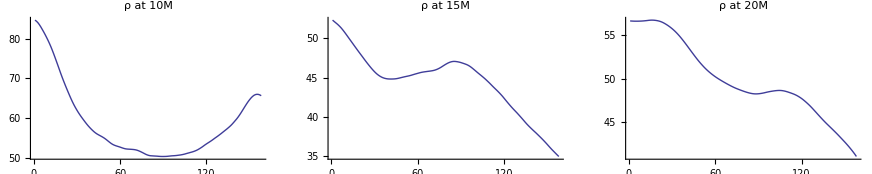

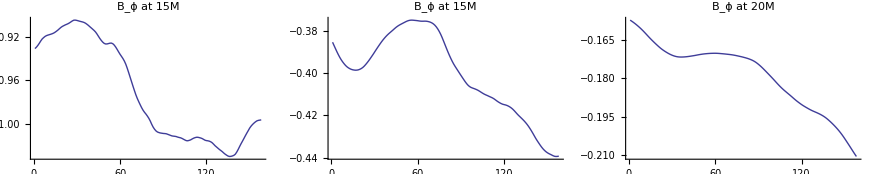

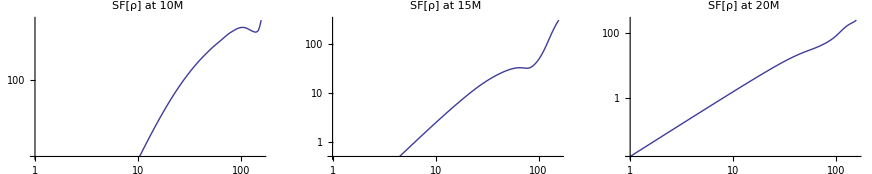

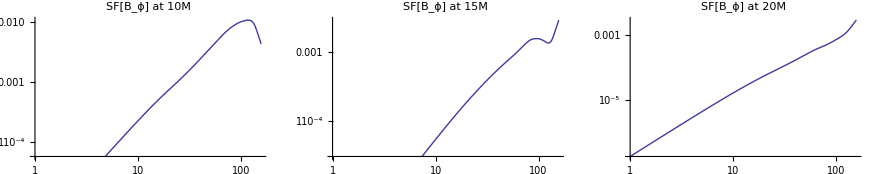

```mathematica
158
```

```mathematica
xf=Total[tab[[All,36;;42,-1]],{2}]/7;xf=Total[tab[[All,43;;53,-1]],{2}];
l=Length[xf];coe=1;
sf=Table[{coe n,Total[((RotateLeft[xf,n]-xf)^2)[[1;;l-n]]]/(l-n)},{n,l-1}];
ListLogLogPlot[sf,Joined->True]
```

```mathematica
Tkep=62*(20/6.)^(3/2)
(2*2(1900-100))/Tkep
```

```mathematica
Dimensions[res2m]
Dimensions[totϕ=Total[res2m,{3}]/32]
Dimensions[totr=Total[totϕ[[sptab[[2,3]];;sptab[[2,3]]+10,All,All]],{1}]]
```

```mathematica
ListLogPlot[Transpose[{θxx,totr[[All,1]]}]]
```

```mathematica
sptab[[2,3]]
```

```mathematica
Dimensions[totθ=Total[totϕ[[All,36;;42,All]],{2}]]
```

```mathematica
rho, u, -u_t, -T^r_t/(rho u^r), u^t, v^r, v^theta, v^phi, B^r, B^theta, B^phi
```

```mathematica
read11[0.98,7000];
```

```mathematica
stt=StringToStream[strrr];
Do[x1min=Read[stt,Number],{i,5}]
Do[dx1=Read[stt,Number],{i,3}]
Do[off=Read[stt,Number],{i,6}]
Close[stt];
rtab=off+Exp[x1min+dx1 Range[0,255]]
np=32;θxx=(h (2x2-1)+(1-h)(2x2-1)^7+1)π/2/.h->0.65/.x2->(x2tab=N[Range[1/(4np),1-1/(4np),1/(2np)]])
```

```mathematica
np=32;θxx=(h (2x2-1)+(1-h)(2x2-1)^7+1)π/2/.h->0.13/.x2->(x2tab=N[Range[1/(4np),1-1/(4np),1/(2np)]])
```

```mathematica
180/π(θxx[[62;;64]]-π/2)
```

```mathematica
Mean[rtab[[63;;73]]]
Mean[rtab[[99;;109]]]
Mean[rtab[[120;;130]]]
Mean[rtab[[135;;145]]]
```

```mathematica
ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.26 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
(240 rg/(2cc))/60/.ruru
(240 rg/(2cc))/(2 60)/.ruru
```